## IGP system with adaptive predator-specific defense and introduced predator

## Replicate Nakazawa by omitting ρ and setting f_i to published values

Define Model

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

### Population & Defense Effort and Fitness Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);

(*fitness is defined as the per capita growth rate of the resource*)
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fP);

(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};

dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
pars = {r-> 1.,k-> 5., c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1., aΝR -> 1., bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1.};
```

#### Manipulate across gradients of k and aPΝ

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};

Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[Delete[pars,Position[Keys[pars],k|aPΝ]],{k->κ,aPΝ->α}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,20},{{α,1,"aPΝ"},0,4}]
```

Solve for equilibria

```mathematica
Get["Figs/temp/equil_Nakazawa.mx"];
```

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,deΝdt == 0,dPdt==0, dePdt==0},{R,Ν, eΝ,P, eP}]];
Save["Figs/temp/equil_Nakazawa.mx",equil];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
(* function to substitute equilibrium densities of a given equilibrium into Jacobian. Works. *)
```

```mathematica
Jeq=J/.equil//Simplify;
```

```mathematica
Jeq3=J/.equil[[3,All]]//FullSimplify;
Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq6=J/.equil[[6,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq17=J/.equil[[17,All]]//FullSimplify;
Jeq21=J/.equil[[21,All]]//FullSimplify;
Jeq23=J/.equil[[23,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq23RΝ=JRΝ/.equil[[23,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
kpars = Delete[pars,Position[Keys[pars],k]];

AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.kpars],#≥0&];
AllFeas4[k_]=AllTrue[Re[equil[[4,All,2]]/.kpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.kpars],#≥0&];
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.kpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.kpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.kpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.kpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.kpars],#≥0&];
AllFeas23[k_]=AllTrue[Re[equil[[23,All,2]]/.kpars],#≥0&];
AllFeas27[k_]=AllTrue[Re[equil[[27,All,2]]/.kpars],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
pReEig3[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 3]]];
pReEig4[k_]=Max[Re[Eigenvalues[N[Jeq4/.kpars], 3]]];
pReEig5[k_]=Max[Re[Eigenvalues[N[Jeq5/.kpars], 3]]];
pReEig6[k_]=Max[Re[Eigenvalues[N[Jeq6/.kpars], 3]]];
pReEig10[k_]=Max[Re[Eigenvalues[N[Jeq10/.kpars],3]]];
pReEig12[k_]=Max[Re[Eigenvalues[N[Jeq12/.kpars],3]]];
pReEig17[k_]=Max[Re[Eigenvalues[N[Jeq17/.kpars],3]]];
pReEig21[k_]=Max[Re[Eigenvalues[N[Jeq21/.kpars], 3]]];
pReEig23[k_]=Max[Re[Eigenvalues[N[Jeq23/.kpars], 3]]];
pReEig27[k_]=Max[Re[Eigenvalues[N[Jeq27/.kpars], 3]]];
```

```mathematica
(*R system*)
```

```mathematica
pReEig3R[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 1]]];
```

```mathematica
(* RN system *)
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.kpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.kpars]]]];
pReEig23RΝ[k_]=Max[Re[Eigenvalues[N[Jeq23RΝ/.kpars]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.kpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.kpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.kpars]]]];
```

Produce plots

### Abundance-gradient plots

#### Across k

```mathematica
(* Functions for species-specific equilibria. Gives value of resource for a given k (and IGP strength) at each euilibrium (which can be specified using the double-brackets) *)
pEquilR[k_]=equil[[All,1,2]]/.kpars//FullSimplify;
pEquilΝ[k_]=equil[[All,2,2]]/.kpars//FullSimplify;
pEquilP[k_]=equil[[All,4,2]]/.kpars//FullSimplify;
pEquileΝ[k_]=equil[[All,3,2]]/.kpars//FullSimplify;
pEquileP[k_]=equil[[All,5,2]]/.kpars//FullSimplify;
```

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Thin,Green},{Thick,Dashed, Green},{Thin, Blue},{Thick, Dashed,Blue},{Thin,Opacity[0.5, Blue]},{Thick, Dashed,Opacity[0.5, Blue]},
{Thin,Red},{Thick,Dashed,Red}, {Thin,Opacity[0.5, Red]},{Thick,Dashed,Opacity[0.5, Red]}};
```

```mathematica
PlotEqR3=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

```mathematica
PlotEqR17=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
PlotEqR17u=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
```

```mathematica
PlotEqR21=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
PlotEqR21u=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]];
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

```mathematica
PlotEqR23=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];
PlotEqR23u=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

```mathematica
Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR23,PlotEqR23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ23=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0.&&AllFeas23[x]]];
PlotEqΝ23u=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0.&&AllFeas23[x]]];
```

```mathematica
Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ23,PlotEqΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ23=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0&&AllFeas23[x]]];
PlotEqeΝ23u=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

```mathematica
Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ23,PlotEqeΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

#### R-RN-RNP-RP

### Invasibility plot (Fig 2.)

#### One equilibrium at a time

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN23 = equil[[23,1,2]];
NstarRN23= equil[[23,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN23 = bPR aPR (1 -0*fP)RstarRN23  + aPN bPΝ NstarRN23 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝpars;
PlotRN17 = Plot[PinvRN17kaPN,{k, 1,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN23 = FullSimplify[Solve[PinvRN23==0,aPN]][[1,1,2]];
PinvRN23kaPN = plotPinvRN23/.kaPΝpars;
PlotRN23 = Plot[PinvRN23kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝpars;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,4,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,4,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,4,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝpars;
PlotRP6 = Plot[Νinv6kaPN,{k, 4,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝpars;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝpars;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN23,PlotRP6,PlotRP10, PlotRP12, PlotRange->Automatic, Frame->True,FrameLabel->{"productivity (k)","IGP stregth (a_PN)"}, AspectRatio -> 1/1, LabelStyle -> Larger]
```

## Introduced Top Predator (P): suboptimal defense toward P

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/IGP-adaptive-defense

### Population & Defense Effort and Fitness Dynamics

```mathematica
(* Subscript[d, i] = (1 - Subscript[e, i] Subscript[f, i]); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) Subscript[e, i]) cost of defense on growth rate of resource *)

dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fΝ ϕ));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fΝ ϕ) R+bPΝ aPΝ Ν - mP);

(*fitness is defined as the per capita growth rate of the resource*)
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fΝ ϕ);

(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

Parameter values

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsCoexM = ReplacePart[parsCoexH,Position[Keys[parsCoexH],ϕ] -> ϕ->  0.75];
parsCoexL = ReplacePart[parsCoexH,Position[Keys[parsCoexH],ϕ] -> ϕ->  0.5];

parsStabϕ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};

dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

#### Manipulate across gradients ϕ

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};

Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[Delete[parsCoexH,Position[Keys[parsCoexH],c0]],{c0 -> χ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{χ,0.2,"c0"},0,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsCoexH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsCoexH,{c0→0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{c0→0.2}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{c0→0.2}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{c0→0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Simulation plots

### Final densities of RNP across relative efficiencies of toward P (ϕ)

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];

(* Note use to 1-ϕ to reverse axis for visualization *)
Off[ParametricNDSolve::prange]

finalϕR = Plot[Evaluate[R[1-ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{1,0},{0,3}}];
finalϕΝ = Plot[Evaluate[Ν[1-ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue}, 
PlotRange->{{1,0},{0,3}}];
finalϕP = Plot[Evaluate[P[1-ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Red}, 
PlotRange->{{1,0},{0,3}}];
finalϕeΝ = Plot[Evaluate[eΝ[1-ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075],Blue, Dashed}, 
PlotRange->{{1,0},{0,3}}];
finalϕeP = Plot[Evaluate[eP[1-ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075],Red, Dashed}, 
PlotRange->{{1,0},{0,3}}];

On[ParametricNDSolve::prange]
```

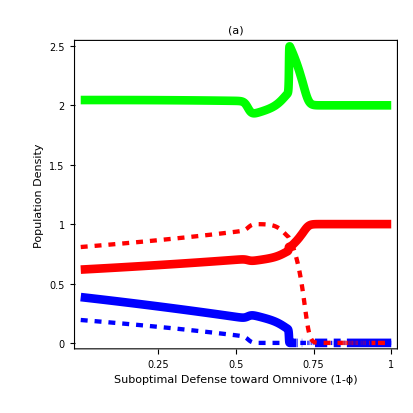

```mathematica
Fig4a = Show[finalϕR,finalϕΝ,finalϕeΝ, finalϕP, finalϕeP,
Frame-> True,
FrameLabel->{"Suboptimal Defense toward Omnivore (1-ϕ)","Population Density", None,"Defense Effort"}, PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, 
FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]

Save["Figs/temp/Fig4a.mx",Fig4a]
```

### Final densities of RNP across productivity gradient for various levels of ϕ

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.
Join[
Delete[parsCoexH,Position[Keys[parsCoexH],k| c0| aPΝ|ϕ ]],{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,10,0.1}, {{χ,0.25,"c0"},0,1,0.05}, {{α,1.2,"aPΝ"},0,4,0.1}, {{Φ,1,"ϕ"},0,1,0.05}]
```

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsCoexH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsCoexH,{k→10.,c0→0.25,aPΝ→0.5,ϕ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{k→10.,c0→0.25,aPΝ→0.5,ϕ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{k→10.,c0→0.25,aPΝ→0.5,ϕ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{k→10.,c0→0.25,aPΝ→0.5,ϕ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexH,Position[Keys[parsCoexH],k ]]},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexM,Position[Keys[parsCoexM],k ]] },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexL,Position[Keys[parsCoexL],k ]]},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];

kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];

kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

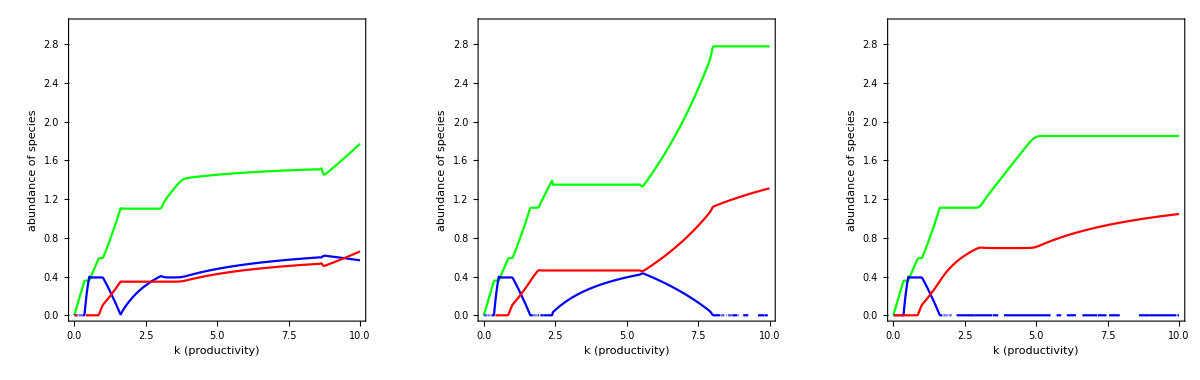

```mathematica
GraphicsGrid[{{
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1, LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}]
```

### Plot final densities across a range of c0

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexH,Position[Keys[parsCoexH],c0 ]]},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexM,Position[Keys[parsCoexM],c0 ]] },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.Delete[parsCoexL,Position[Keys[parsCoexL],c0 ]]},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

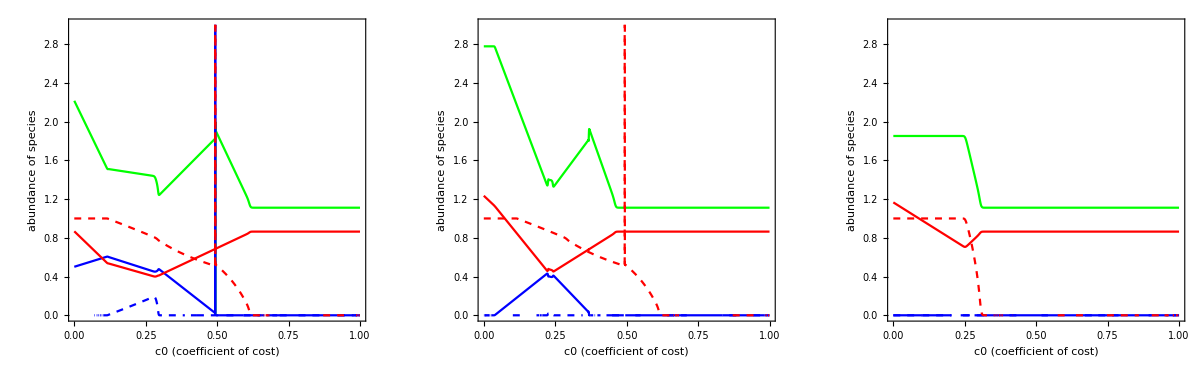

```mathematica
GraphicsGrid[{{Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}]
```

Solve for equilibria

```mathematica
Get["Figs/temp/equil_suboptP.mx"];
```

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
Save["Figs/temp/equil_suboptP.mx",equil];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1 | R→0 | Ν→0 | P→0 | eΝ→1-eP | 
2 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-eP | 
3 | R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
4 | R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | eP→0
5 | R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
6 | R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
7 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
8 | R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
9 | R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
10 | R→-(k (aΝR mP+aPΝ bPΝ (-1+c0) r+aPR bPΝ mΝ (-1+fΝ ϕ)))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ)) | Ν→(-aPR k (-1+fΝ ϕ) (aΝR bΝR mP+aPR bPR mΝ (-1+fΝ ϕ))+aPΝ (mP-aPR bPR (-1+c0) k r (-1+fΝ ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bPΝ bΝR (-1+c0) r+aPR bPR mΝ (-1+fΝ ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fΝ ϕ))) | eΝ→0 | eP→1
11 | R→mP/(aPR bPR-aPR bPR fΝ ϕ) | Ν→0 | P→(-mP+aPR bPR (-1+c0) k r (-1+fΝ ϕ))/(aPR^2 bPR k (-1+fΝ ϕ)^2) | eΝ→0 | eP→1
12 | R→-(k r (c0+c0 ϕ-fΝ ϕ))/(fΝ ϕ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→-(aPΝ c0 r+aPR fΝ mΝ ϕ+aPR aΝR bΝR k r (c0+c0 ϕ-fΝ ϕ))/(aPR aΝR bΝR fΝ k r (fΝ ϕ-c0 (1+ϕ))) | eP→(-aΝR fΝ mP ϕ+aPΝ bPΝ c0 r ϕ-aPR aΝR bPR k r (c0+c0 ϕ-fΝ ϕ))/(aPR aΝR bPR fΝ k r ϕ (fΝ ϕ-c0 (1+ϕ)))
13 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-1/(fΝ ϕ)+mP/(aPR bPR fΝ k r ϕ-aPR bPR c0 fΝ k r ϕ) | eP→(mP-aPR bPR k r+aPR bPR c0 k r)/(-aPR bPR fΝ k r ϕ+aPR bPR c0 fΝ k r ϕ)
14 | R→(k (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r ϕ+aΝR bΝR mP (1+ϕ-fΝ ϕ)+aPR bPR mΝ ϕ (1+ϕ-fΝ ϕ)))/(aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2) | Ν→(ϕ (-aPR bPR mΝ ϕ+aΝR bΝR (-mP+aPR bPR (-1+c0) k r (-1+(-1+fΝ) ϕ))))/(aΝR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2)) | P→(-aPR bPR mΝ ϕ+aΝR bΝR (-mP+aPR bPR (-1+c0) k r (-1+(-1+fΝ) ϕ)))/(aPR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fΝ ϕ)^2)) | eΝ→(aPR aΝR k (-1+(-1+fΝ) ϕ) (aΝR bΝR mP+aPR bPR mΝ (-1+fΝ ϕ))-aPΝ (aPR bPΝ mΝ ϕ+aΝR (mP+aPR (-1+c0) k r (bPR+bPΝ bΝR ϕ-bPR fΝ ϕ))))/(aPR aΝR fΝ k (aΝR bΝR mP (-1+(-1+fΝ) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (-1+(-1+fΝ) ϕ)))) | eP→(aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-1+(-1+fΝ) ϕ)+aPΝ (aPR bPΝ mΝ ϕ+aΝR (mP+aPR (-1+c0) k r (bPR-bPΝ bΝR (-1+fΝ) ϕ))))/(aPR aΝR fΝ k (aΝR bΝR mP (-1+(-1+fΝ) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aPR bPR mΝ (-1+(-1+fΝ) ϕ))))
15 | R→(aPΝ c0 r+aPR fΝ mΝ ϕ)/(aPR aΝR bΝR fΝ ϕ) | Ν→-(aPΝ c0 r+aPR fΝ mΝ ϕ+aPR aΝR bΝR k r (c0-fΝ ϕ))/(aPR aΝR^2 bΝR fΝ k ϕ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→((-aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k)/(aPR aΝR fΝ k ϕ)+(bΝR (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ c0 r+aPR fΝ mΝ ϕ))/bPR
16 | R→k r (1-c0/(fΝ ϕ)) | Ν→0 | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→1/(fΝ ϕ)+mP/(aPR bPR c0 k r-aPR bPR fΝ k r ϕ)
17 | R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
18 | R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
19 | R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | P→0 | eΝ→1 | eP→0
20 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
21 | R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | eP→0
22 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
23 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
24 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
25 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
26 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
27 | R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
28 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]/.{eP-> 0, P-> 0}//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]/.{eΝ-> 0, Ν -> 0}//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν+aPR P (-1+eP fΝ ϕ) | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | aPR R (-1+eP fΝ ϕ) | R (-c0 r+aPR fΝ P ϕ)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v | v (c0 (-1+eP+2 eΝ) r+aΝR fΝ (Ν-2 eΝ Ν)-aPR eP fΝ P ϕ) | -aPR eP eΝ fΝ v ϕ | eΝ v (c0 r-aPR fΝ P ϕ)
aPR bPR P (1-eP fΝ ϕ) | aPΝ bPΝ P | 0 | -mP+aPΝ bPΝ Ν+aPR bPR R (1-eP fΝ ϕ) | -aPR bPR fΝ P R ϕ
0 | -aΝR eP eΝ fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (-1+eP) eP fΝ v ϕ | v (c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν+aPR (1-2 eP) fΝ P ϕ))

(r-c0 eΝ r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v | (-1+2 eΝ) v (c0 r-aΝR fΝ Ν))

(r-c0 eP r-(2 R)/k+aPR P (-1+eP fΝ ϕ) | aPR R (-1+eP fΝ ϕ) | R (-c0 r+aPR fΝ P ϕ)
aPR bPR P (1-eP fΝ ϕ) | -mP+aPR bPR R (1-eP fΝ ϕ) | -aPR bPR fΝ P R ϕ
0 | -aPR (-1+eP) eP fΝ v ϕ | (-1+2 eP) v (c0 r-aPR fΝ P ϕ))

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
subparsH=Delete[parsCoexH,Position[Keys[parsCoexH],c0 ]];
subparsM=Delete[parsCoexM,Position[Keys[parsCoexM],c0 ]];
subparsL=Delete[parsCoexL,Position[Keys[parsCoexL],c0 ]];
```

```mathematica
(*R system*)
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsH],#≥0&];
AllFeas9[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsH],#≥0&];
AllFeas11[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsH],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];

AllFeas9M[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[c0_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[c0_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.subparsH]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];

pReEig17RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsH]]]];
pReEig16RP[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsH]]]];
pReEig11RP[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsH]]]];

pReEig9RPM[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[c0_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[c0_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[c0_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH =Delete[parsCoexH,Position[Keys[parsCoexH],c0|aPΝ ]];
c0aPΝparsM= Delete[parsCoexM,Position[Keys[parsCoexM],c0|aPΝ ]];
c0aPΝparsL= Delete[parsCoexL,Position[Keys[parsCoexL],c0|aPΝ ]];
```

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

-mP+(aPR bPR mΝ)/(aΝR bΝR)+(aPN bPΝ (-mΝ/(bΝR k)+aΝR r))/aΝR^2

-mP+(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR (-c0+fΝ) k r)/fΝ

-mP+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)+(aPN bPΝ (-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r))/(aΝR^2 bΝR (-1+fΝ)^2 k)

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ
```

(aΝR bΝR mP)/(aPR bPR)-mΝ-(aPΝ (-mP/(bPR k)+aPR r))/aPR^2

-mΝ+aΝR bΝR k r (1-c0/(fΝ ϕ))-(aPΝ c0 r)/(aPR fΝ ϕ)

-mΝ+(aΝR bΝR mP)/(aPR bPR-aPR bPR fΝ ϕ)-(aPΝ (-mP+aPR bPR (-1+c0) k r (-1+fΝ ϕ)))/(aPR^2 bPR k (-1+fΝ ϕ)^2)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,k]][[1,1,2]];
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,
PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsH;
Jeq=J/.equil/.c0aPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3aReg= RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig3aReg.mx",Fig3aReg]
```

$Aborted

```mathematica
Fig3a =Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21, PlotRN17a, PlotRN21a,PlotRN19,Fig3aReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.8}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1",FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}}, 
FrameTicks->{{{0,1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
Save["Figs/temp/Fig3a.mx",Fig3a]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom,  FillingStyle-> GrayLevel[0.5],
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom,  FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN+0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.8],
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsM;
Jeq=J/.equil/.c0aPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3bReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig3bReg.mx",Fig3bReg]
```

$Aborted

```mathematica
Fig3b = Show[PlotRP9,PlotRP16, PlotRP11, PlotRN17, PlotRN21,PlotRN17a, PlotRN21a,PlotRN19, Fig3bReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.28,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(b)    ϕ = 0.75",FontSize->14,  Bold], 
FrameTicks->{{{0,1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
Save["Figs/temp/Fig3b.mx",Fig3b]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.c0aPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.c0aPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,40}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.c0aPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];

(*P invades*)

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.c0aPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PlotRN17a = Plot[PinvRN17kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN-0.02}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{c0, 0,1},  PlotRange->{{0,1},{Νinv9kaPN + 0.02,4}} ,
PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PlotRN21a = Plot[PinvRN21kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv9kaPN - 0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White,
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.c0aPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsL;
Jeq=J/.equil/.c0aPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3cReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig3cReg.mx",Fig3cReg]
```

```mathematica
Fig3c= Show[PlotRP9,PlotRP16, PlotRP11,PlotRN17, PlotRN21,PlotRN17a,PlotRN21a,PlotRN19,Fig3cReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.48,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True,AspectRatio -> 1/1, 
PlotRange->{{0,1},{0,2}},
FrameTicks->{{{0,1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
Save["Figs/temp/Fig3c.mx",Fig3c]
```

Produce Plots across k

## Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subparsH=Delete[parsCoexH,Position[Keys[parsCoexH],k ]];
subparsM=Delete[parsCoexM,Position[Keys[parsCoexM],k ]];
subparsL=Delete[parsCoexL,Position[Keys[parsCoexL],k ]];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsH],#≥0&];
AllFeas11[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsH],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];

AllFeas9M[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];

pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsH]]]];
pReEig16RP[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsH]]]];
pReEig11RP[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsH]]]];

pReEig9RPM[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH=Delete[parsCoexH,Position[Keys[parsCoexH],k|aPΝ ]];
kaPΝparsM=Delete[parsCoexM,Position[Keys[parsCoexH],k|aPΝ ]];
kaPΝparsL=Delete[parsCoexL,Position[Keys[parsCoexH],k|aPΝ ]];
```

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP
```

-mP+(aPR bPR mΝ)/(aΝR bΝR)+(aPN bPΝ (-mΝ/(bΝR k)+aΝR r))/aΝR^2

-mP+(aPN bPΝ c0 r)/(aΝR fΝ)+(aPR bPR (-c0+fΝ) k r)/fΝ

-mP+(aPR bPR mΝ)/(aΝR bΝR-aΝR bΝR fΝ)+(aPN bPΝ (-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r))/(aΝR^2 bΝR (-1+fΝ)^2 k)

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN17kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.kaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> {White},  
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.kaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.kaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];
```

```mathematica
equilP= equil/.kaPΝparsH;
Jeq=J/.equil/.kaPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

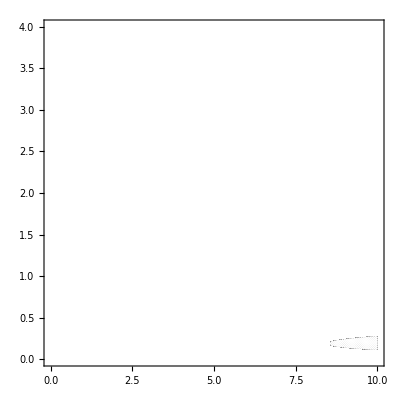

```mathematica
Fig2aReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}];
Save["Figs/temp/Fig2aReg.mx",Fig2aReg]
```

```mathematica
Fig2a = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Fig2aReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.15}]]
}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.25,0.14}],Scaled[{0.08,0.1}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.85,0.9}],Scaled[{0.98,0.9}]}]}],
PlotLabel -> Style["ϕ = 1, ρ = 1", FontSize->12,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
FrameTicks->{{{0,1,2,3, 4},{None}},{{0, 5, 10}, {None}}}]
Save["Figs/temp/Fig2a.mx",Fig2a]
```

-Graphics-

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN17kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

```mathematica
equilP= equil/.kaPΝparsM;
Jeq=J/.equil/.kaPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

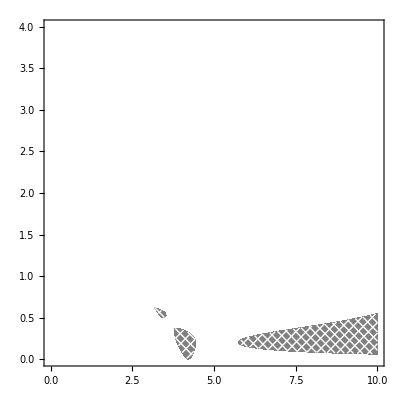

```mathematica
Fig2bReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}];
Save["Figs/temp/Fig2bReg.mx",Fig2bReg]
```

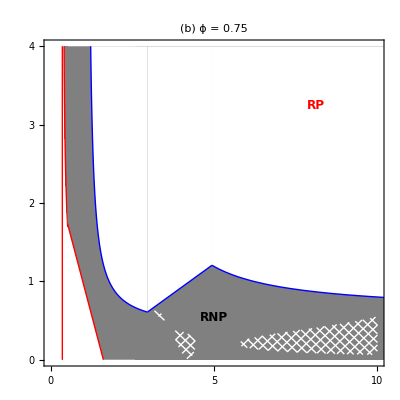

```mathematica
Fig2b = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Fig2bReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
FrameTicks->{{{0,1,2,3, 4},{None}},{{0, 5, 10}, {None}}}]
Save["Figs/temp/Fig2b.mx",Fig2b]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN17kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];
```

```mathematica
equilP= equil/.kaPΝparsL;
Jeq=J/.equil/.kaPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

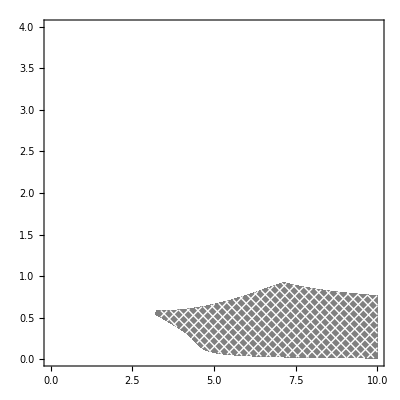

```mathematica
Fig2cReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}];
Save["Figs/temp/Fig2cReg.mx",Fig2cReg]
```

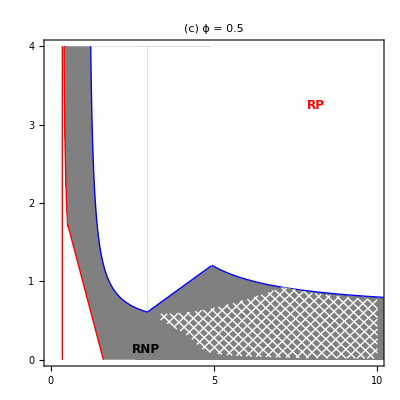

```mathematica
Fig2c = Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Fig2cReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.3,0.05}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.8,0.8}]]}],
(*Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.25,0.28}],Scaled[{0.1,0.11}]}]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.3,0.28}],Scaled[{0.36,0.04}]}]}],*)
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
FrameTicks->{{{0,1,2,3, 4},{None}},{{0, 5, 10}, {None}}}]
Save["Figs/temp/Fig2c.mx",Fig2c]
```

Multipanel of resource and single predator across c0

```mathematica
c0parsRN=Join[Delete[parsCoexH,Position[Keys[parsCoexH],c0|k|aPΝ|aΝR| bΝR]],{k-> 1, aPΝ-> 1, aΝR-> 1.5,bΝR-> 0.8}];
```

### Functions for working with equilibrium values across a gradient of cost (c0)

```mathematica
pEquilR[c0_]=equil[[All,1,2]]/.c0parsRN//FullSimplify;
pEquilΝ[c0_]=equil[[All,2,2]]/.c0parsRN//FullSimplify;
pEquileΝ[c0_]=equil[[All,4,2]]/.c0parsRN//FullSimplify;
```

```mathematica
Jeq3R=J/.equil[[3,All]]//FullSimplify;Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.c0parsRN],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.c0parsRN],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.c0parsRN],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.c0parsRN],#≥0&];
```

```mathematica
pReEig3R[c0_]=Max[Re[Eigenvalues[N[Jeq3R/.c0parsRN]]]]; 
pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.c0parsRN]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.c0parsRN]]]];
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.c0parsRN]]]];
```

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Green, Thickness[0.015]},{Thickness[0.005],Dashed, Opacity[0.5, Green]},{Thickness[0.015], Blue},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},{Thickness[0.005],Opacity[0.5, Blue]},{Thickness[0.005], Dashed,Opacity[0.5, Blue]},
{Thickness[0.015],Red},{Thickness[0.005],Dashed,Opacity[0.5, Red]}, {Thickness[0.015],Opacity[0.5, Red]},{Thickness[0.005],Dashed,Opacity[0.5, Red]},  {Thickness[0.015],Purple},  {Thickness[0.005],Dashed,Opacity[0.5, Purple]}, {Thickness[0.005],Dashed, Opacity[0.5, Black] }};
```

```mathematica
PlotEqR3=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

```mathematica
PlotEqR17=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]]
PlotEqR17u=Plot[{pEquilR[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]]
```

```mathematica
PlotEqR21=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]]
PlotEqR21u=Plot[{pEquilR[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]]
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

```mathematica
PlotEqR19=Plot[{pEquilR[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]]
PlotEqR19u=Plot[{pEquilR[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]]
```

```mathematica
Fig1a = Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR19,PlotEqR19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(a)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},LabelStyle->{Black, Larger},Spacings-> 30,
FrameLabel->{None,"Resource Abundance"},Frame->True,RotateLabel->True]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ19=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0.&&AllFeas19[x]]];
PlotEqΝ19u=Plot[{pEquilΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,3}}, PlotStyle->ELineCols[[6]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0.&&AllFeas19[x]]];
```

```mathematica
Fig1b = Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ19,PlotEqΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(b)                                                                                 ",  FontSize->14,  Bold],
GridLines -> {{0.132, 0.667}, {0}},
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
FrameLabel->{None,"Consumer Abundance"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[c0][[3]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[c0][[17]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[c0][[21]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ19=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig19RΝ[x]< 0&&AllFeas19[x]]];
PlotEqeΝ19u=Plot[{pEquileΝ[c0][[19]]},{c0,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->ELineCols[[12]], RegionFunction->Function[{x},pReEig19RΝ[x]≥0&&AllFeas19[x]]];

Fig1c = Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ19,PlotEqeΝ19u,PlotRange->{{0,1}, {0,1.2}},
PlotLabel -> Style["(c)                                                                                 ",  FontSize->14,  Bold],
FrameTicks->{{0.25, 0.5, 0.75, 1},{0, 0.5, 1},{None}, {None}},
GridLines -> {{0.132, 0.667}, {0}},
FrameLabel->{None,"Defense Effort"},LabelStyle->{Black, Larger},
Frame->True,RotateLabel->True]

Fig1 = Panel[GraphicsColumn[{Fig1a,Fig1b,Fig1c},  ImageSize-> 432, Spacings->0], 
{"Cost of Defense",Rotate["",Pi/2]},
{Bottom,Left},Background->White, LabelStyle->Larger]
Save["Figs/temp/Fig1.mx",Fig1]
```

## Plot ϕ against IGP strength (not useful)

### Functions for working with equilibrium values across a gradient of productivity (ϕ)

```mathematica
parsCoexc0L = Join[Delete[parsCoexM,Position[Keys[parsCoexM],c0|k]],{k-> 6, c0-> 0.1}];
parsCoexc0M=Join[Delete[parsCoexM,Position[Keys[parsCoexM],c0|k]],{k-> 6, c0-> 0.3}];
parsCoexc0H=Join[Delete[parsCoexH,Position[Keys[parsCoexH],c0|k]],{k-> 6, c0-> 0.5}];
```

```mathematica
subparsL=Delete[parsCoexc0L,Position[Keys[parsCoexc0L],ϕ]];
subparsM=Delete[parsCoexc0M,Position[Keys[parsCoexc0M],ϕ]];
subparsH=Delete[parsCoexc0H,Position[Keys[parsCoexc0H],ϕ]];
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
AllFeas9L[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];

AllFeas9M[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9H[ϕ_]=AllTrue[Re[equil[[9,All,2]]/.subparsH],#≥0&];
AllFeas11H[ϕ_]=AllTrue[Re[equil[[11,All,2]]/.subparsH],#≥0&];
AllFeas16H[ϕ_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];
AllFeas17H[ϕ_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19H[ϕ_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];
AllFeas21H[ϕ_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];
```

```mathematica
pReEig17RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];

pReEig17RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]]; 
pReEig21RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig19RΝH[ϕ_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];
```

```mathematica
pReEig9RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];

pReEig9RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsH]]]];
pReEig16RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsH]]]];
pReEig11RPH[ϕ_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsH]]]];
```

### Invasibility Plot (ϕ and aPN)

#### P invades RN

```mathematica
ϕaPΝparsL = Delete[parsCoexc0L,Position[Keys[parsCoexc0L],aPΝ|ϕ]];
ϕaPΝparsM = Delete[parsCoexc0M,Position[Keys[parsCoexc0M],aPΝ|ϕ]];
ϕaPΝparsH = Delete[parsCoexc0H,Position[Keys[parsCoexc0H],aPΝ|ϕ]];
```

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
```

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}]
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]]

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig16RPL[x]< 0&&AllFeas16L[x]]]

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]]
```

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

#### Medium cost (c0 = 0.5)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.ϕaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.ϕaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];

Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, PlotRange->{{0,1},{0,2}}]
```

#### High cost (c0 = 0.75)

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.ϕaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}];

plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.ϕaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> None, FillingStyle-> {Gray},  
RegionFunction->Function[{x},pReEig9RPH[x]< 0&&AllFeas9H[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.ϕaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig16RPH[x]<0&&AllFeas16H[x]]];

plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.ϕaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{ϕ, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> None, FillingStyle-> {Gray},
RegionFunction->Function[{x},pReEig11RPH[x]<0&&AllFeas11H[x]]];

Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True,  PlotRange->{{0,1},{0,2}},LabelStyle-> Larger]
```

## Introduced Top Predator (P): naivete toward P

Define Model

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/IGP-adaptive-defense

### Population & Defense Effort and Fitness Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);

(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) - ρ aPR P (1 - eP fP);

(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

Parameter values

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8, fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
parsCoexM =  ReplacePart[parsCoexH,Position[Keys[parsCoexH],ρ] -> ρ->  0.75];
parsCoexL =  ReplacePart[parsCoexH,Position[Keys[parsCoexH],ρ] -> ρ->  0.5];

parsStabρ = {r-> 0.9,k-> 5, c0->0.1, fΝ->0.7,  fP->0.7,aPR-> 0.5, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.6, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.25, v-> 1};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};

dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

#### Manipulate across ρ

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[Delete[parsCoexH,Position[Keys[parsCoexH],ρ ]],{ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,10000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Ρ,0.5,"ρ"},0,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsCoexH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsCoexH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsCoexH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsCoexH,{ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kparsρH = Delete[parsCoexH,Position[Keys[parsCoexH],k ]];
kparsρM = ReplacePart[kparsρH,Position[Keys[kparsρH],ρ] -> ρ->  0.75];
kparsρL =ReplacePart[kparsρH,Position[Keys[kparsρH],ρ] -> ρ->  0.5];
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝH = Plot[Evaluate[eΝ[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePH = Plot[Evaluate[eP[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝM = Plot[Evaluate[eΝ[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePM = Plot[Evaluate[eP[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝL = Plot[Evaluate[eΝ[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePL= Plot[Evaluate[eP[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

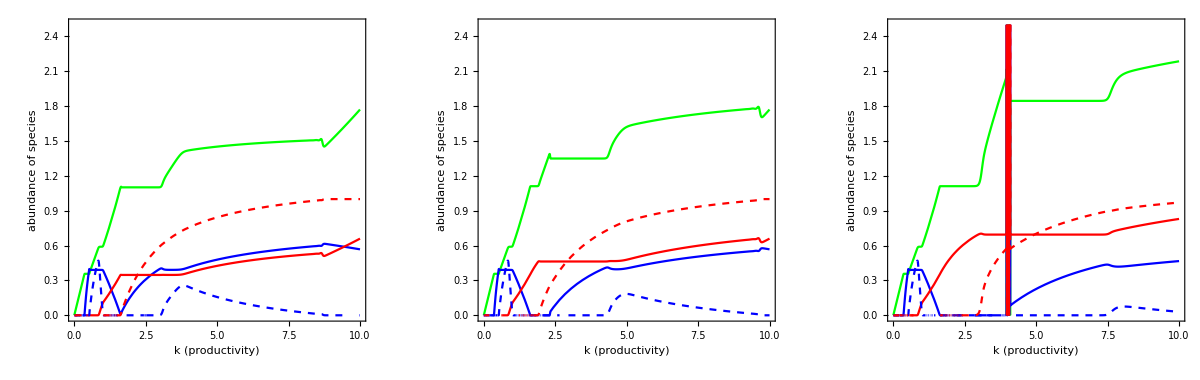

```mathematica
GraphicsGrid[{{
Show[kfinalRH,kfinalΝH,kfinalPH,kfinaleΝH, kfinalePH, Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRM,kfinalΝM, kfinalPM,kfinaleΝM, kfinalePM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRL,kfinalΝL,kfinalPL,kfinaleΝL, kfinalePL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}]
```

### Final Densities across cost

```mathematica
c0parsρH = Delete[parsCoexH,Position[Keys[parsCoexH],c0 ]];
c0parsρM = ReplacePart[c0parsρH,Position[Keys[c0parsρH],ρ] -> ρ->  0.75];
c0parsρL =ReplacePart[c0parsρH,Position[Keys[c0parsρH],ρ] -> ρ->  0.5];
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρH},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,2.5}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,2.5}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,2.5}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
c0finalePL= Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

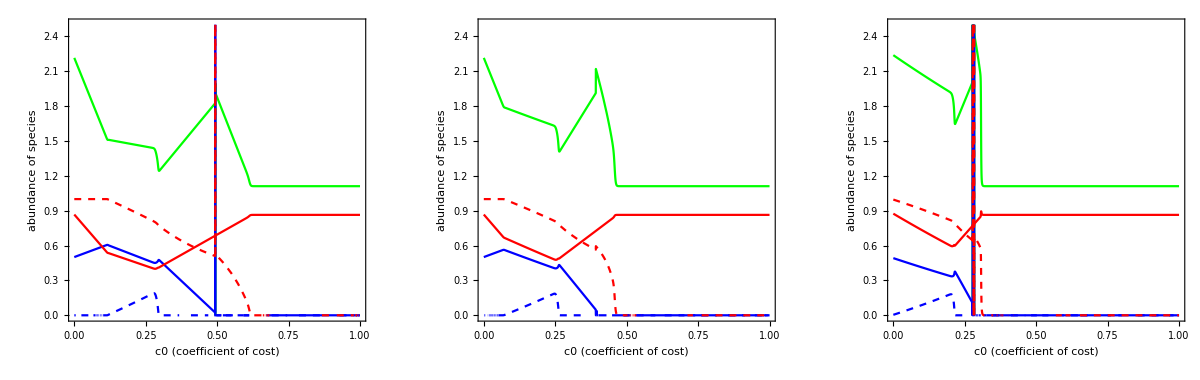

```mathematica
GraphicsGrid[{{
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePM, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}]
```

### Final densities of RNP across relative efficiencies of toward P (ρ)

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabρ},{R,Ν, P, eΝ, eP},{t,0,10000}, {ρ}];

(* Note use to 1-ρ to reverse axis for visualization *)
Off[ParametricNDSolve::prange]

finalρR = Plot[Evaluate[R[1-ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{0,1},{0,3}}];
finalρΝ = Plot[Evaluate[Ν[1-ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Blue},
PlotRange->{{0,1},{0,3}}];
finalρP = Plot[Evaluate[P[1-ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Red},
PlotRange->{{0,1},{0,3}}];
finalρeΝ = Plot[Evaluate[eΝ[1-ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle->{Thickness[0.0075],Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
finalρeP = Plot[Evaluate[eP[1-ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.0075],Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];

On[ParametricNDSolve::prange]
```

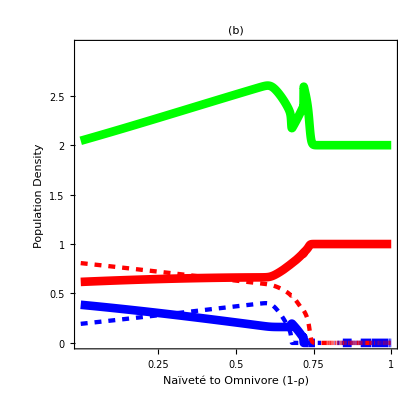

```mathematica
Fig4b =Show[finalρR,finalρΝ,finalρeΝ, finalρP, finalρeP,
Frame-> True,
FrameLabel->{"Naïveté to Omnivore (1-ρ)","Population Density", "","Defense Effort"}, 
PlotLabel -> Style["(b)                                                                                       ", FontSize->14,  Bold],
ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, 
FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{0,0.5,1, 1.5, 2, 2.5}},{{1, 0.75, 0.5,0.25}, {None}}}]
Save["Figs/temp/Fig4b.mx",Fig4b]
```

Solve for equilibria

```mathematica
Get["Figs/temp/equil_naiveP.mx"];
```

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
Save["Figs/temp/equil_naiveP.mx",equil];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-eP | 
2 | R→0 | Ν→0 | P→0 | eΝ→1-eP | 
3 | R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
4 | R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | eP→0
5 | R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aPR aΝR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aPR aΝR bPR (-c0+fΝ) k r)/(aPR^2 aΝR bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ (aPΝ bPΝ c0+aPR aΝR (bPΝ bΝR c0+bPR (-c0+fΝ)) k) r)/(aPR aΝR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
6 | R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
7 | R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
8 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
9 | R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
10 | R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(-mP+aPR bPR (-1+c0) (-1+fP) k r)/(aPR^2 bPR (-1+fP)^2 k) | eΝ→0 | eP→1
11 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-1/fP+mP/(aPR bPR fP k r-aPR bPR c0 fP k r) | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
12 | R→-(c0 k r-fP k r-(√k √r √(-4 c0 fP mP+(4 c0 fP mP+aPR bPR (c0-fP)^2 k r) ρ))/(√aPR √bPR √ρ))/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(c0 (-2+ρ)+fP ρ-(√ρ √(-4 c0 fP mP+(4 c0 fP mP+aPR bPR (c0-fP)^2 k r) ρ))/(√aPR √bPR √k √r))/(2 c0 fP (-1+ρ))
13 | R→-(c0 k r-fP k r+(√k √r √(-4 c0 fP mP+(4 c0 fP mP+aPR bPR (c0-fP)^2 k r) ρ))/(√aPR √bPR √ρ))/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(c0 (-2+ρ)+fP ρ+(√ρ √(-4 c0 fP mP+(4 c0 fP mP+aPR bPR (c0-fP)^2 k r) ρ))/(√aPR √bPR √k √r))/(2 c0 fP (-1+ρ))
14 | R→(-aPR^2 aΝR bPR fP (fP (-1+fΝ)-fΝ) k mΝ (bPR+bPΝ bΝR (-2+ρ)) ρ+aPR aΝR fΝ k (-aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ)^2+aΝR bΝR (-fP+(-1+fP) fΝ) mP (bPR-2 bPR ρ+bPΝ bΝR ρ))+(-bPR+bPΝ bΝR ρ) √(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2))))/(2 aPR aΝR (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | Ν→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ (-bPR+bPΝ bΝR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) ρ (-aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2)))))/(2 aPΝ aΝR fΝ (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | P→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (-bPR+bPΝ bΝR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) (-aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2)))))/(2 aPR aPΝ fP (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | eΝ→(aPR^2 aΝR bPR fP k mΝ ((-1+fP) fΝ (-2+ρ)+fP ρ)+aPR aΝR fΝ k (aΝR bΝR mP (fΝ-fP (1+fΝ-2 ρ))-aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ))+√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPΝ aΝR fΝ (mP+aPR bPR (-1+c0) k r)+aPR aPΝ bPΝ fP (mΝ+aΝR bΝR (-1+c0+fΝ-c0 fΝ) k r) ρ+aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-fΝ+fP (-1+fΝ) ρ))+aPR aΝR k (-aPΝ (-1+c0) fP fΝ r (bPR-bPΝ bΝR ρ)+aPR bPR fP mΝ (fP ρ-fΝ (-2+ρ+fP ρ))+aΝR bΝR fΝ mP (fΝ+fP (-1+fΝ+2 ρ-2 fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ)) | eP→(aPR^2 aΝR bPR fP k mΝ (-fP ρ+fΝ (-2+ρ+fP ρ))+aPR aΝR fΝ k (aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ)+aΝR bΝR mP (-fΝ+fP (-1+fΝ) (-1+2 ρ)))-√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPΝ aΝR fΝ (mP+aPR bPR (-1+c0) k r)+aPR aPΝ bPΝ fP (mΝ+aΝR bΝR (-1+c0+fΝ-c0 fΝ) k r) ρ+aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-fΝ+fP (-1+fΝ) ρ))+aPR aΝR k (-aPΝ (-1+c0) fP fΝ r (bPR-bPΝ bΝR ρ)+aPR bPR fP mΝ (fP ρ-fΝ (-2+ρ+fP ρ))+aΝR bΝR fΝ mP (fΝ+fP (-1+fΝ+2 ρ-2 fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ))
15 | R→(-aPR^2 aΝR bPR fP (fP (-1+fΝ)-fΝ) k mΝ (bPR+bPΝ bΝR (-2+ρ)) ρ+aPR aΝR fΝ k (-aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ)^2+aΝR bΝR (-fP+(-1+fP) fΝ) mP (bPR-2 bPR ρ+bPΝ bΝR ρ))+(bPR-bPΝ bΝR ρ) √(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2))))/(2 aPR aΝR (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | Ν→-(ρ (aPΝ fP fΝ (-2 aPR bPR fP mΝ+aΝR bΝR (-2 fΝ mP+aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (-bPR+bPΝ bΝR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) (aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2))))))/(2 aPΝ aΝR fΝ (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | P→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (-bPR+bPΝ bΝR ρ)-bPR bΝR (fP (-1+fΝ)-fΝ) (aPR aΝR (fP (-1+fΝ)-fΝ) k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aPR aΝR k (aPR aPΝ^2 aΝR (-1+c0)^2 fP^2 fΝ^2 k r^2 (bPR-bPΝ bΝR ρ)^2+aPR aΝR (fP+fΝ-fP fΝ)^2 k (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+2 aPΝ fP fΝ (aΝR fΝ mP (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r))+(-2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR fΝ mP-aPR bPΝ fP mΝ)+aPR aΝR (-1+c0) (-fP+(-1+fP) fΝ) k (aΝR bΝR (2 bPR-bPΝ bΝR) fΝ mP+aPR bPR (bPR-2 bPΝ bΝR) fP mΝ) r) ρ-aPR bPΝ fP mΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ^2)))))/(2 aPR aPΝ fP (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPR-bPΝ bΝR ρ)^2)) | eΝ→(aPR^2 aΝR bPR fP k mΝ ((-1+fP) fΝ (-2+ρ)+fP ρ)+aPR aΝR fΝ k (aΝR bΝR mP (fΝ-fP (1+fΝ-2 ρ))-aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ))-√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPΝ aΝR fΝ (mP+aPR bPR (-1+c0) k r)+aPR aPΝ bPΝ fP (mΝ+aΝR bΝR (-1+c0+fΝ-c0 fΝ) k r) ρ+aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-fΝ+fP (-1+fΝ) ρ))+aPR aΝR k (-aPΝ (-1+c0) fP fΝ r (bPR-bPΝ bΝR ρ)+aPR bPR fP mΝ (fP ρ-fΝ (-2+ρ+fP ρ))+aΝR bΝR fΝ mP (fΝ+fP (-1+fΝ+2 ρ-2 fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ)) | eP→(aPR^2 aΝR bPR fP k mΝ (-fP ρ+fΝ (-2+ρ+fP ρ))+aPR aΝR fΝ k (aPΝ (-1+c0) fP r (bPR-bPΝ bΝR ρ)+aΝR bΝR mP (-fΝ+fP (-1+fΝ) (-1+2 ρ)))+√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPΝ aΝR fΝ (mP+aPR bPR (-1+c0) k r)+aPR aPΝ bPΝ fP (mΝ+aΝR bΝR (-1+c0+fΝ-c0 fΝ) k r) ρ+aPR aΝR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ) (-fΝ+fP (-1+fΝ) ρ))+aPR aΝR k (-aPΝ (-1+c0) fP fΝ r (bPR-bPΝ bΝR ρ)+aPR bPR fP mΝ (fP ρ-fΝ (-2+ρ+fP ρ))+aΝR bΝR fΝ mP (fΝ+fP (-1+fΝ+2 ρ-2 fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ))
16 | R→(-aPR aΝR bPR fP (-fP fΝ+c0 (fP+fΝ)) k r ρ+√(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR fP^2 fΝ ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→-(aPR^2 aΝR bPR fP^2 (-fP fΝ+c0 (fP+fΝ)) k mΝ r ρ^2+aPΝ c0 r √(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ))+aPR fP ρ (aΝR c0 k r (aPΝ r (-bPR fP fΝ+bPR c0 (fP+fΝ)+2 bPΝ bΝR c0 fP (-1+ρ))-2 aΝR bΝR fP fΝ mP (-1+ρ))+mΝ √(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ))))/(2 aPR aΝR bΝR c0 fP^2 fΝ k r (aΝR fΝ mP-aPΝ bPΝ c0 r) (-1+ρ) ρ) | eP→(aPR aΝR bPR fP k r (c0 fΝ (-2+ρ)-c0 fP ρ+fP fΝ ρ)-√(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR c0 fP^2 fΝ k r (-1+ρ))
17 | R→-(aPR aΝR bPR fP (-fP fΝ+c0 (fP+fΝ)) k r ρ+√(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR fP^2 fΝ ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→(-aPR^2 aΝR bPR fP^2 (-fP fΝ+c0 (fP+fΝ)) k mΝ r ρ^2+aPΝ c0 r √(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ))+aPR fP ρ (aΝR c0 k r (-aPΝ r (-bPR fP fΝ+bPR c0 (fP+fΝ)+2 bPΝ bΝR c0 fP (-1+ρ))+2 aΝR bΝR fP fΝ mP (-1+ρ))+mΝ √(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ))))/(2 aPR aΝR bΝR c0 fP^2 fΝ k r (aΝR fΝ mP-aPΝ bPΝ c0 r) (-1+ρ) ρ) | eP→(aPR aΝR bPR fP k r (c0 fΝ (-2+ρ)-c0 fP ρ+fP fΝ ρ)+√(aPR aΝR bPR fP^2 k r ρ (-4 aΝR c0 fP fΝ^2 mP-4 aPΝ bPΝ c0^2 fP fΝ r (-1+ρ)+aΝR (4 c0 fP fΝ^2 mP+aPR bPR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR c0 fP^2 fΝ k r (-1+ρ))
18 | R→-(k (aΝR mP+aPR bPΝ (-1+fP) mΝ+aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k) | Ν→(-aPR (-1+fP) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)+aPΝ (mP+aPR bPR (-1+c0+fP-c0 fP) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eΝ→0 | eP→1
19 | R→(aPΝ c0 r+aPR fP mΝ ρ)/(aPR aΝR bΝR fP ρ) | Ν→(-aPΝ^2 bPR c0^2 r^2+aPR aPΝ bPR c0 r (-2 fP mΝ+aΝR bΝR (-c0+fP) k r) ρ+aPR fP ρ (-aPR bPR fP mΝ^2 ρ+aΝR bΝR k r (aΝR bΝR c0 mP (-1+ρ)+aPR bPR (-c0+fP) mΝ ρ)))/(aPR aΝR^2 bΝR fP k ρ (aPΝ c0 r (bPR+bPΝ bΝR (-1+ρ))+aPR bPR fP mΝ ρ)) | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(-aPΝ c0 (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) r+aPR fP (-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r)) ρ)/(aPR aΝR fP k (aPΝ c0 r (bPR+bPΝ bΝR (-1+ρ))+aPR bPR fP mΝ ρ))
20 | R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
21 | R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
22 | R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | P→0 | eΝ→1 | eP→0
23 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
24 | R→((-c0+fΝ) k r)/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→1/fΝ+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r) | eP→0
25 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
26 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
27 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
28 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
29 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
30 | R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
31 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm;
JRΝ//MatrixForm;
JRP//MatrixForm;
```

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subparsH=Delete[parsCoexH,Position[Keys[parsCoexH],k ]];
subparsM=Delete[parsCoexM,Position[Keys[parsCoexM],k ]];
subparsL=Delete[parsCoexL,Position[Keys[parsCoexL],k ]];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq20RΝ=JRΝ/.equil[[20,All]]//FullSimplify;
Jeq24RΝ=JRΝ/.equil[[24,All]]//FullSimplify;
Jeq22RΝ=JRΝ/.equil[[22,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsH],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsH],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsH],#≥0&];
AllFeas20[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsH],#≥0&];
AllFeas22[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsH],#≥0&];
AllFeas24[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsH],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
pReEig20RΝ[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsH]]]]; 
pReEig24RΝ[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsH]]]];
pReEig22RΝ[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsH]]]];

pReEig20RΝM[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsH]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsH]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsH]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH= Delete[parsCoexH,Position[Keys[parsCoexH],k|aPΝ ]];
kaPΝparsM=Delete[parsCoexM,Position[Keys[parsCoexM],k|aPΝ ]];
kaPΝparsL=Delete[parsCoexL,Position[Keys[parsCoexL],k|aPΝ ]];
```

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP;
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.kaPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.kaPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.kaPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,10}, PlotRange->{{0,10},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

```mathematica
equilP= equil/.kaPΝparsH;
Jeq=J/.equil/.kaPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig2aaReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}]
(* Save["Figs/temp/Fig2aaReg.mx",Fig2aaReg]*)
```

```mathematica
Fig2aa = Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10, Fig2aaReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.5,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.22,0.9}]], 
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.35,0.05}]]}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.05,0.02}]}]}],
Graphics[{Red,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.8,0.9}],Scaled[{0.96,0.9}]}]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],Frame->True, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
FrameTicks->{{{0,1,2,3, 4},{None}},{{None}, {None}}}]
(*Save["Figs/temp/Fig2aa.mx",Fig2aa]*)
```

#### Medium naivete (ρ = 0.75)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN20kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];
```

```mathematica
equilP= equil/.kaPΝparsM;
Jeq=J/.equil/.kaPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig2dReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}];
Save["Figs/temp/Fig2dReg.mx",Fig2dReg]
```

$Aborted

```mathematica
Fig2d=Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP10,Fig2dReg,
Graphics[{
Text[Style["RNP",12,Black , Bold],Scaled[{0.6,0.5}]],
Text[Style["RN",12,Blue,Bold],Scaled[{0.3,0.07}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]]
(*, 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]*)
}],
Graphics[{Blue,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.22,0.05}],Scaled[{0.08,0.02}]}]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
FrameTicks->{{{0,1,2,3, 4},{None}},{{0, 5, 10}, {None}}}]
Save["Figs/temp/Fig2d.mx",Fig2d]
```

-Graphics-

#### Low relative efficiency (ρ = 0.5)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsL;
PlotRN20L = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN20kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsL;
PlotRN24L = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsL;
PlotRN22L = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsL;
PlotRP12L = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];
```

```mathematica
equilP= equil/.kaPΝparsL;
Jeq=J/.equil/.kaPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig2eReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,10},{aPΝ,0,4},
Mesh->25,MeshFunctions->{#1+2.5#2&,#1-2.5#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,10},{0,4}}];
Save["Figs/temp/Fig2eReg.mx",Fig2eReg]
```

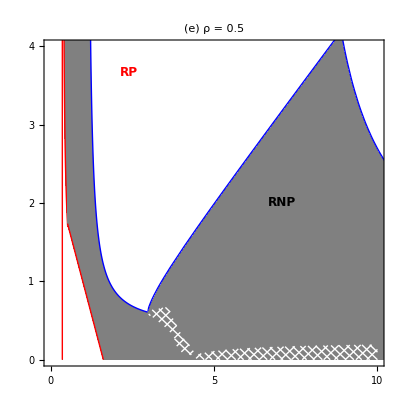

```mathematica
Fig2e =Show[PlotRN20L, PlotRN24L,PlotRN22L,PlotRP6L,PlotRP12L, PlotRP10L,Fig2eReg,
Graphics[{
Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.5}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.25,0.9}]]
(*, 
Text[Style["RP",12,Red , Bold],Scaled[{0.93,0.9}]]*)
}],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold], 
FrameTicks->{{{0,1,2,3, 4},{None}},{{0, 5, 10}, {None}}}]
Save["Figs/temp/Fig2e.mx",Fig2e]
```

```mathematica
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.1}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}];
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.225}]}]}];
```

```mathematica
igpO=
Show[
Graphics[{{GrayLevel[0],Thickness[0.05],
Line[{{0.1, 0.1},{.6,.6}}], 
Line[{{0.6, 0.6},{0,1}}], 
Line[{{0.1, 0.1},{0,1}}] 
}}],
Graphics[{{GrayLevel[0.5],Disk[{.1,.1},.2]},{GrayLevel[0.5], Disk[{.6,.6},.2]}, {GrayLevel[0.5],Disk[{0,1.0},.2]}, {Red,Thickness[0.04],Circle[{0,1.0},.18]}, 
{Black,Thickness[0.01],Circle[{0.1,0.1},.2]}, 
{Black,Thickness[0.01],Circle[{0.6,0.6},.2]}}],
Graphics[{Text[Style["R",16,Black , Bold],{0.1,0.1}], 
Text[Style["N",16,Black , Bold],{0.6,0.6}],
Text[Style["P",16,Black , Bold],{0,1}]}]]
Save["Figs/temp/igpO.mx",igpO]
```

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
subparsH=Delete[parsCoexH,Position[Keys[parsCoexH],c0 ]];
subparsM=Delete[parsCoexM,Position[Keys[parsCoexM],c0 ]];
subparsL=Delete[parsCoexL,Position[Keys[parsCoexL],c0 ]];
```

```mathematica
AllFeas6[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsH],#≥0&];
AllFeas10[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsH],#≥0&];
AllFeas12[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsH],#≥0&];
AllFeas20[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsH],#≥0&];
AllFeas22[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsH],#≥0&];
AllFeas24[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsH],#≥0&];

AllFeas6M[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas10M[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas12M[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas10L[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas12L[c0_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[c0_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[c0_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[c0_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig20RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsH]]]]; 
pReEig24RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsH]]]];
pReEig22RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsH]]]];

pReEig20RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
pReEig6RP[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsH]]]];
pReEig12RP[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsH]]]];
pReEig10RP[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsH]]]];

pReEig6RPM[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig10RPM[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];

pReEig6RPL[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[c0_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig10RPL[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH= Delete[parsCoexH,Position[Keys[parsCoexH],c0|aPΝ ]];
c0aPΝparsM=Delete[parsCoexM,Position[Keys[parsCoexM],c0|aPΝ ]];
c0aPΝparsL=Delete[parsCoexL,Position[Keys[parsCoexL],c0|aPΝ ]];
```

### Invasibility Plot (k and aPN)

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPΝ bPΝ NstarRN20 - mP;
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPΝ bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPΝ bPΝ NstarRN22 - mP;
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]]
Νinv6kaPN = plotΝinv6/.c0aPΝparsH
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]]
Νinv10kaPN = plotΝinv10/.c0aPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsH;
Jeq=J/.equil/.c0aPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3aaReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
(*Save["Figs/temp/Fig3aaReg.mx",Fig3aaReg]*)
```

```mathematica
Fig3aa = Show[PlotRP6,PlotRP12, PlotRP10,PlotRN20, PlotRN24,PlotRN22, Fig3aaReg,
Frame->True, AspectRatio -> 1/1];
(*Save["Figs/temp/Fig3aa.mx",Fig3aa]*)
```

#### Medium recognition (ρ = 0.75)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsM;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsM;
Jeq=J/.equil/.c0aPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3dReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig3dReg.mx",Fig3dReg]
```

```mathematica
Fig3d =Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24,PlotRN20a, PlotRN24a,PlotRN22,Fig3dReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold], 
FrameTicks->{{{ 0,1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
Save["Figs/temp/Fig3d.mx",Fig3d]
```

#### Low recognition (ρ = 0.5)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.c0aPΝparsL
PlotRP6 = Plot[Νinv6kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.c0aPΝparsL;
PlotRP12 = Plot[Νinv12kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,2.2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.c0aPΝparsL;
PlotRP10 = Plot[Νinv10kaPN,{c0, -1,1}, PlotRange->{{-1,1},{-10,10}} ,PlotStyle->{Blue, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],   
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPΝ]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.c0aPΝparsL;
PlotRN20 = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PlotRN20a = Plot[PinvRN20kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPΝ]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.c0aPΝparsL;
PlotRN24 = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{Νinv6kaPN +0.02,4}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> GrayLevel[0.8], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PlotRN24a = Plot[PinvRN24kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,Νinv6kaPN -0.02}} ,PlotStyle->{Red, Thick},
Filling-> Bottom, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPΝ]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.c0aPΝparsL;
PlotRN22 = Plot[PinvRN22kaPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Bottom, FillingStyle-> GrayLevel[0.5],  
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsL;
Jeq=J/.equil/.c0aPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig3eReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{2#1+#2&,2#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig3eReg.mx",Fig3eReg]
```

```mathematica
Fig3e=Show[PlotRP6,PlotRP12, PlotRP10, PlotRN20, PlotRN24, PlotRN20a, PlotRN24a,PlotRN22,Fig3eReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.15}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.75,0.8}]], 
Text[Style["RN",12,Blue, Bold ],Scaled[{0.85,0.1}]],
Text[Style["RN/RP",9,Black, Bold ],Scaled[{0.75,0.4}]]}],
Graphics[{Black,Thickness[0.005],Arrowheads[0.08],
Arrow[{Scaled[{0.75,0.37}],Scaled[{0.9,0.26}]}]}],
Graphics[{Blue,Thick,
Line[{{0.3217,0.72},{0.3217,0.49}}]}],
Frame->True,AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},
PlotLabel -> Style["(e)    ρ = 0.5",FontSize->14,  Bold], 
FrameTicks->{{{ 0,1,2},{None}},{{0,0.5,1}, {None}}}, FrameTicksStyle-> Smaller]
Save["Figs/temp/Fig3e.mx",Fig3e]
```

## Introduced Intermediate Consumer (Ν): suboptimal defense toward Ν

Define Model

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/IGP-adaptive-defense

### Population & Defense Effort and Fitness Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fP ϕ)- aPR P (1 - eP fP ));
dΝdt = Ν (bΝR aΝR (1- eΝ fP ϕ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);

(*fitness is defined as the per capita growth rate of the resource*)
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fP ϕ) -  aPR P (1 - eP fP);

(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

Parameter values

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fP->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};

parsExcH = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> 0.4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
parsExcM =  ReplacePart[parsExcH,Position[Keys[parsExcH],ϕ] -> ϕ->  0.75];
parsExcL=  ReplacePart[parsExcH,Position[Keys[parsExcH],ϕ] -> ϕ->  0.45];

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ϕ->1};
parsFacN = {r-> 1,k-> 0.28, c0->0.125, fP->0.8,  aPR-> 0.9, aPΝ -> 1.7, aΝR -> 0.8, bPΝ->0.5, bΝR->1, bPR->0.5, mP->0.35, mΝ->0.1, v-> 1, ϕ->1};

parsGoodH =  {r->1,k->3,c0->0.1,fP->0.6,aPR->1,aPΝ->0.8,aΝR->0.8,bPΝ->0.5,bΝR->0.9,bPR->0.4,mP->0.55,mΝ->0.1,v->1, ϕ-> 1};
parsGoodM =  ReplacePart[parsGoodH,Position[Keys[parsGoodH],ϕ] -> ϕ->  0.75];
parsGoodL=  ReplacePart[parsGoodH,Position[Keys[parsGoodH],ϕ] -> ϕ->  0.5];
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};

dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

#### Manipulate across gradient of k and others

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[Delete[parsGoodH,Position[Keys[parsGoodH],k|c0|aPΝ|ϕ|bΝR | mP]],{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ, bΝR-> β, mP-> μ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,0.28,"k"},0,10}, {{χ,0.15,"c0"},0,1},{{α,1.5,"aPΝ"},0,2}, 
{{β,1,"bΝR"},0,1}, {{μ,.3,"mP"},0,1},{{Φ,1,"ϕ"},0,1}]
```

#### Comparison Plots

```mathematica
parsGoodϕ =  Delete[parsGoodH,Position[Keys[parsGoodH],ϕ]];

finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsGoodϕ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ϕ}];

(* Note use to 1-ϕ to reverse axis for visualization *)
Off[ParametricNDSolve::prange]

Rfinalϕ = Plot[Evaluate[R[1-ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,1},{0,2}}];
Νfinalϕ = Plot[Evaluate[Ν[1-ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,1},{0,2}}];
Pfinalϕ = Plot[Evaluate[P[1-ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,1},{0,2}}];
eΝfinalϕ = Plot[Evaluate[eΝ[1-ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075],Blue, Dashed}, 
PlotRange->{{0,1},{0,2}}];
ePfinalϕ = Plot[Evaluate[eP[1-ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075], Red, Dashed}, 
PlotRange->{{0,1},{0,2}}];

On[ParametricNDSolve::prange]
```

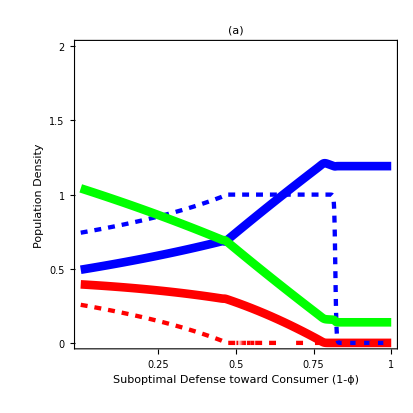

```mathematica
Fig7a = Show[Νfinalϕ,Pfinalϕ,eΝfinalϕ, ePfinalϕ,Rfinalϕ, Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer (1-ϕ)","Population Density", "","Defense Effort"}, ImageSize -> 414,Spacings-> 30,
PlotLabel -> Style["(a)                                                                                       ", FontSize->14,  Bold],
AspectRatio -> 1/1, ImageSize -> 414,Spacings -> 30,LabelStyle-> {Black, Larger}, 
FrameTicks->{{{0,0.5,1, 1.5, 2},{0.5,1, 1.5, 2}},{{1, 0.75, 0.5, 0.25}, {None}}}]
Save["Figs/temp/Fig7a.mx",Fig7a]
```

```mathematica
parsFacNϕ = Delete[parsFacN,Position[Keys[parsFacN],ϕ]];

finalFacϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsFacNϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];

(* Note use to 1-ϕ to reverse axis for visualization *)
Off[ParametricNDSolve::prange]

RfinalϕFac = Plot[Evaluate[R[1-ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Green}, 
PlotRange->{{0,0.28},{0,1}}];
ΝfinalϕFac = Plot[Evaluate[Ν[1-ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.015], Blue},  
PlotRange->{{0,0.28},{0,1}}];
PfinalϕFac = Plot[Evaluate[P[1-ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle->  {Thickness[0.015], Red},  
PlotRange->{{0,0.28},{0,1}}];
eΝfinalϕFac = Plot[Evaluate[eΝ[1-ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075],Blue, Dashed}, 
PlotRange->{{0,0.28},{0,1}}];
ePfinalϕFac = Plot[Evaluate[eP[1-ϕ][500]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thickness[0.0075], Red, Dashed}, 
PlotRange->{{0,0.28},{0,1}}];

Off[ParametricNDSolve::prange]
```

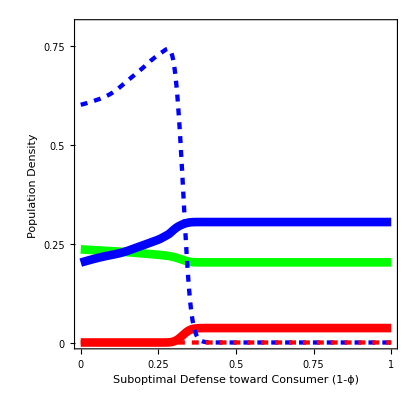

```mathematica
Fig8=Show[RfinalϕFac,ΝfinalϕFac,PfinalϕFac,eΝfinalϕFac, ePfinalϕFac, 
Frame-> True, FrameLabel->{"Suboptimal Defense toward Consumer (1-ϕ)","Population Density", "","Defense Effort"}, 
ImageSize -> 414,Spacings-> 30, 
AspectRatio -> 1/1, LabelStyle-> {Black, Larger}, 
PlotRange-> {{0,1},{0,0.8}},
FrameTicks->{{{0,0.25,0.5,0.75,1},
{0,0.25,0.5,0.75,1}},{{0,0.25, 0.5,0.75,1}, {None}}}]
Save["Figs/temp/Fig8.mx",Fig8]
```

### PLot final densities across a range of c0

```mathematica
c0parsϕH = Delete[parsExcH,Position[Keys[parsExcH],c0]];
c0parsϕM = Delete[parsExcM,Position[Keys[parsExcM],c0]];
c0parsϕL = Delete[parsExcL,Position[Keys[parsExcL],c0]];
```

```mathematica
c0finalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {c0}];
c0finalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
c0finalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.c0parsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {c0}];
```

```mathematica
c0finalRH = Plot[Evaluate[R[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝH = Plot[Evaluate[Ν[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPH = Plot[Evaluate[P[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝH = Plot[Evaluate[eΝ[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePH = Plot[Evaluate[eP[c0][500]/.c0finalH,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRM = Plot[Evaluate[R[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝM = Plot[Evaluate[Ν[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPM = Plot[Evaluate[P[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝM = Plot[Evaluate[eΝ[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePM = Plot[Evaluate[eP[c0][500]/.c0finalM,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
c0finalRL = Plot[Evaluate[R[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Green, 
PlotRange->{{0,1},{0,3}}];
c0finalΝL  = Plot[Evaluate[Ν[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Blue, 
PlotRange->{{0,1},{0,3}}];
c0finalPL  = Plot[Evaluate[P[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> Red, 
PlotRange->{{0,1},{0,3}}];
c0finaleΝL = Plot[Evaluate[eΝ[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,3}}];
c0finalePL = Plot[Evaluate[eP[c0][500]/.c0finalL,{c0,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,3}}];
```

```mathematica
GraphicsGrid[{{
Show[c0finalRH,c0finalΝH,c0finalPH,c0finaleΝH, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRM,c0finalΝM,c0finalPM,c0finaleΝM, c0finalePH, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[c0finalRL,c0finalΝL,c0finalPL,c0finaleΝL, c0finalePL, Frame-> True, FrameLabel-> {"c0 (coefficient of cost)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}
```

Determine equilibria

```mathematica
Get["Figs/temp/equil_suboptN.mx"];
```

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
Save["Figs/temp/equil_suboptN.mx",equil];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1 | R→0 | Ν→0 | P→0 | eP→1-eΝ | 
2 | R→-(-1+c0) k r | Ν→0 | P→0 | eP→1-eΝ | 
3 | R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
4 | R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
5 | R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(-mP+aPR bPR (-1+c0) (-1+fP) k r)/(aPR^2 bPR (-1+fP)^2 k) | eΝ→0 | eP→1
6 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-1/fP+mP/(aPR bPR fP k r-aPR bPR c0 fP k r) | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
7 | R→((-c0+fP) k r)/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→1/fP+mP/(aPR bPR c0 k r-aPR bPR fP k r)
8 | R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
9 | R→-(k (aΝR mP+aPR bPΝ (-1+fP) mΝ+aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k) | Ν→(-aPR (-1+fP) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)+aPΝ (mP+aPR bPR (-1+c0+fP-c0 fP) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eΝ→0 | eP→1
10 | R→(aPR fP mΝ+aPΝ c0 r)/(aPR aΝR bΝR fP) | Ν→(-aPR fP mΝ-aPΝ c0 r+aPR aΝR bΝR (-c0+fP) k r)/(aPR aΝR^2 bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPR fP (-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ))+aPΝ (-aPΝ bPΝ c0+aPR aΝR (bPR c0+bPΝ bΝR (-c0+fP)) k) r)/(aPR aΝR bPR fP k (aPR fP mΝ+aPΝ c0 r))
11 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
12 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
13 | R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
14 | R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
15 | R→(k (aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r+aΝR mP (-1+fP ϕ)))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fP ϕ)) | Ν→(aPΝ (mP+aPR bPR (-1+c0) k r)-aPR k (aPR bPR mΝ+aΝR bΝR mP (-1+fP ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fP ϕ))) | P→-(aPΝ bPΝ mΝ+aΝR k (-1+fP ϕ) (aPR bPR mΝ-aPΝ bPΝ bΝR (-1+c0) r+aΝR bΝR mP (-1+fP ϕ)))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) k (-1+fP ϕ))) | eΝ→1 | eP→0
16 | R→mΝ/(aΝR bΝR-aΝR bΝR fP ϕ) | Ν→(-mΝ+aΝR bΝR (-1+c0) k r (-1+fP ϕ))/(aΝR^2 bΝR k (-1+fP ϕ)^2) | P→0 | eΝ→1 | eP→0
17 | R→-(k r (c0+c0 ϕ-fP ϕ))/(fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(c0 r)/(aPR fP) | eΝ→-(aPR fP mΝ ϕ+aPΝ c0 r ϕ+aPR aΝR bΝR k r (c0+c0 ϕ-fP ϕ))/(aPR aΝR bΝR fP k r ϕ (fP ϕ-c0 (1+ϕ))) | eP→(aPΝ bPΝ c0 r-aΝR (fP mP ϕ+aPR bPR k r (c0+c0 ϕ-fP ϕ)))/(aPR aΝR bPR fP k r (fP ϕ-c0 (1+ϕ)))
18 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(mΝ-aΝR bΝR k r+aΝR bΝR c0 k r)/(-aΝR bΝR fP k r ϕ+aΝR bΝR c0 fP k r ϕ) | eP→1-1/(fP ϕ)+mΝ/(aΝR bΝR fP k r ϕ-aΝR bΝR c0 fP k r ϕ)
19 | R→(k (-aPΝ (bPR-bPΝ bΝR) (-1+c0) r ϕ+aPR bPR mΝ (1+ϕ-fP ϕ)+aΝR bΝR mP ϕ (1+ϕ-fP ϕ)))/(aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fP ϕ)^2) | Ν→(-aΝR bΝR mP ϕ+aPR bPR (-mΝ+aΝR bΝR (-1+c0) k r (-1+(-1+fP) ϕ)))/(aΝR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fP ϕ)^2)) | P→(ϕ (-aΝR bΝR mP ϕ+aPR bPR (-mΝ+aΝR bΝR (-1+c0) k r (-1+(-1+fP) ϕ))))/(aPR (aPΝ (bPR-bPΝ bΝR) ϕ+aPR aΝR bPR bΝR k (1+ϕ-fP ϕ)^2)) | eΝ→(-aPΝ aΝR mP ϕ+aPR^2 aΝR bPR (-1+fP) k mΝ (-1+(-1+fP) ϕ)+aPR (-aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP (-1+(-1+fP) ϕ)+aPΝ (-1+c0) r (-bPΝ bΝR+bPR (-1+fP) ϕ))))/(aPR aΝR fP k (aPR bPR mΝ (-1+(-1+fP) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aΝR bΝR mP (-1+(-1+fP) ϕ)))) | eP→(aPΝ aΝR mP ϕ+aPR^2 aΝR bPR k mΝ (-1+(-1+fP) ϕ)+aPR (aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP (-1+(-1+fP) ϕ) (-1+fP ϕ)+aPΝ (-1+c0) r (bPΝ bΝR+bPR ϕ-bPΝ bΝR fP ϕ))))/(aPR aΝR fP k (aPR bPR mΝ (-1+(-1+fP) ϕ)+ϕ (aPΝ (bPR-bPΝ bΝR) (-1+c0) r+aΝR bΝR mP (-1+(-1+fP) ϕ))))
20 | R→(-aPΝ bPΝ c0 r+aΝR fP mP ϕ)/(aPR aΝR bPR fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(aPΝ bPΝ c0 r-aΝR (fP mP ϕ+aPR bPR k r (c0-fP ϕ)))/(aPR^2 aΝR bPR fP k ϕ) | eΝ→((aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)/(aPR aΝR fP k ϕ)+(bPR (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ c0 r-aΝR fP mP ϕ))/(bPΝ bΝR) | eP→0
21 | R→k r (1-c0/(fP ϕ)) | Ν→(c0 r)/(aΝR fP ϕ) | P→0 | eΝ→1/(fP ϕ)+mΝ/(aΝR bΝR c0 k r-aΝR bΝR fP k r ϕ) | eP→0
22 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
23 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
24 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
25 | R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
26 | R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
27 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
28 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR Ν (-1+eΝ fP ϕ) | aΝR R (-1+eΝ fP ϕ) | R (-c0 r+aΝR fP Ν ϕ) | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aΝR bΝR Ν (1-eΝ fP ϕ) | -mΝ-aPΝ P+aΝR bΝR R (1-eΝ fP ϕ) | -aΝR bΝR fP R Ν ϕ | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fP v ϕ | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fP Ν ϕ) | -aPR eP eΝ fP v | eΝ (-aPR fP P+c0 r) v
aPR bPR (1-eP fP) P | aPΝ bPΝ P | 0 | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aΝR eP eΝ fP v ϕ | eP v (c0 r-aΝR fP Ν ϕ) | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fP Ν ϕ))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR Ν (-1+eΝ fP ϕ) | aΝR R (-1+eΝ fP ϕ) | R (-c0 r+aΝR fP Ν ϕ)
aΝR bΝR Ν (1-eΝ fP ϕ) | -mΝ-aPΝ P+aΝR bΝR R (1-eΝ fP ϕ) | -aΝR bΝR fP R Ν ϕ
0 | -aΝR (-1+eΝ) eΝ fP v ϕ | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fP Ν ϕ))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR Ν (-1+eΝ fP ϕ) | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aPR bPR (1-eP fP) P | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fP Ν ϕ))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subparsH=Delete[parsExcH,Position[Keys[parsExcH],k]];
subparsM=Delete[parsExcM,Position[Keys[parsExcM],k]];
subparsL=Delete[parsExcL,Position[Keys[parsExcL],k]];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq14RΝ=JRΝ/.equil[[14,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq16RΝ=JRΝ/.equil[[16,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq3RP=JRP/.equil[[3,All]]//FullSimplify;
Jeq7RP=JRP/.equil[[7,All]]//FullSimplify;
Jeq5RP=JRP/.equil[[5,All]]//FullSimplify;
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsH],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsH],#≥0&];
AllFeas7[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsH],#≥0&];
AllFeas14[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsH],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];

AllFeas3M[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig14RΝ[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsH]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig16RΝ[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsH]]]];

pReEig14RΝM[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig3RP[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsH]]]];
pReEig7RP[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsH]]]];
pReEig5RP[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsH]]]];

pReEig3RPM[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

Produce Plots

```mathematica
kaPΝparsH=Delete[parsExcH,Position[Keys[parsExcH],k|aPΝ]];
kaPΝparsM=Delete[parsExcM,Position[Keys[parsExcM],k|aPΝ]];
kaPΝparsL=Delete[parsExcL,Position[Keys[parsExcL],k|aPΝ]];
```

```mathematica
RstarRN14 = equil[[14,1,2]];
NstarRN14= equil[[14,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN16 = equil[[16,1,2]];
NstarRN16= equil[[16,2,2]];
```

```mathematica
PinvRN14 = bPR aPR (1 -0*fP)RstarRN14  + aPN bPΝ NstarRN14 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN16 = bPR aPR (1 -0*fP)RstarRN16  + aPN bPΝ NstarRN16 - mP;
```

#### High Efficiency

```mathematica
plotPinvRN14 = FullSimplify[Solve[PinvRN14==0,aPN]][[1,1,2]];
PinvRN14kaPN = plotPinvRN14/.kaPΝparsH;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], Exclusions->{Solve[Denominator[PinvRN14kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN16 = FullSimplify[Solve[PinvRN16==0,aPN]][[1,1,2]];
PinvRN16kaPN = plotPinvRN16/.kaPΝparsH;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];
```

```mathematica
Rstar3 = equil[[3,1,2]];
Pstar3= equil[[3,3,2]];
Rstar7 = equil[[7,1,2]];
Pstar7= equil[[7,3,2]];
Rstar5 = equil[[5,1,2]];
Pstar5= equil[[5,3,2]];
```

```mathematica
Νinv3 = bΝR aΝR (1 -0*fΝ)Rstar3  - aPΝ Pstar3 - mΝ;
Νinv7 = bΝR aΝR (1 -0*fΝ)Rstar7  - aPΝ Pstar7 - mΝ;
Νinv5= bΝR aΝR (1 -0*fΝ)Rstar5 - aPΝ Pstar5 - mΝ;
```

```mathematica
plotΝinv3= FullSimplify[Solve[Νinv3==0,aPΝ]][[1,1,2]];
Νinv3kaPN = plotΝinv3/.kaPΝparsH;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.1112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White, AspectRatio -> 1/1, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

plotΝinv7= FullSimplify[Solve[Νinv7==0,aPΝ]][[1,1,2]];
Νinv7kaPN = plotΝinv7/.kaPΝparsH;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

plotΝinv5= FullSimplify[Solve[Νinv5==0,aPΝ]][[1,1,2]];
Νinv5kaPN = plotΝinv5/.kaPΝparsH;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

```mathematica
equilP= equil/.kaPΝparsH;
Jeq=J/.equil/.kaPΝparsH/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0/.{ComplexInfinity-> 0, Indeterminate-> 0};
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. k ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Fig5aReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0,eΝ-> 0,ComplexInfinity-> 0, Indeterminate-> 0}]]],
{k,0,5},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,5},{0,2}}];
Save["Figs/temp/Fig5aReg.mx",Fig5aReg]
```

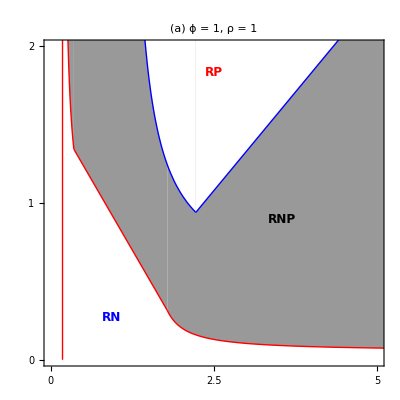

```mathematica
Fig5a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig5aReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.2,0.15}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,2.5,5}, {None}}}]
Save["Figs/temp/Fig5a.mx",Fig5a]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsM;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], Exclusions->{Solve[Denominator[PinvRN14kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsM;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3kaPN = plotΝinv3/.kaPΝparsM;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig3RPM[x]< 0&&AllFeas3M[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsM;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsM;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

```mathematica
equilP= equil/.kaPΝparsM;
Jeq=J/.equil/.kaPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig5bReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,5},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,5},{0,2}}];
Save["Figs/temp/Fig5bReg.mx",Fig5bReg]
```

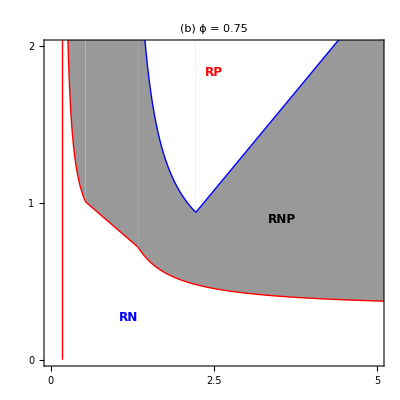

```mathematica
Fig5b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig5bReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,2.5,5}, {None}}}]
Save["Figs/temp/Fig5b.mx",Fig5b]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsL;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,1.112}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], Exclusions->{Solve[Denominator[PinvRN14kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 1.112,1.85}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsL;
PlotRN16 = Plot[PinvRN16kaPN,{k, 1.85,6}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6]];

Νinv3kaPN = plotΝinv3/.kaPΝparsL;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White,AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig3RPL[x]< 0&&AllFeas3L[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsL;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsL;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

```mathematica
equilP= equil/.kaPΝparsL;
Jeq=J/.equil/.kaPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig5cReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,5},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,5},{0,2}}];
Save["Figs/temp/Fig5cReg.mx",Fig5cReg]
```

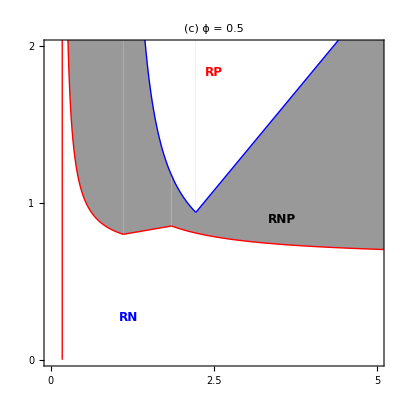

```mathematica
Fig5c= Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig5cReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,2.5,5}, {None}}}]
Save["Figs/temp/Fig5c.mx",Fig5c]
```

## Plot cost against IGP strength

### Functions for working with equilibrium values across a gradient of productivity (c0)

```mathematica
subparsH=Delete[parsExcH,Position[Keys[parsExcH],c0]];
subparsM=Delete[parsExcM,Position[Keys[parsExcM],c0]];
subparsL=Delete[parsExcL,Position[Keys[parsExcL],c0]];
```

```mathematica
AllFeas3[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsH],#≥0&];
AllFeas5[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsH],#≥0&];
AllFeas7[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsH],#≥0&];
AllFeas14[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsH],#≥0&];
AllFeas21[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsH],#≥0&];
AllFeas16[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsH],#≥0&];

AllFeas3M[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[c0_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[c0_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[c0_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[c0_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[c0_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[c0_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];

pReEig14RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsH]]]]; 
pReEig21RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsH]]]];
pReEig16RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsH]]]];

pReEig14RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
pReEig3RP[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsH]]]];
pReEig7RP[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsH]]]];
pReEig5RP[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsH]]]];

pReEig3RPM[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[c0_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[c0_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[c0_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

### Invasibility Plot (c0 and aPN)

#### P invades RN

```mathematica
c0aPΝparsH =Delete[parsExcH,Position[Keys[parsExcH],c0|aPΝ]];
c0aPΝparsM=Delete[parsExcM,Position[Keys[parsExcM],c0|aPΝ]];
c0aPΝparsL=Delete[parsExcL,Position[Keys[parsExcL],c0|aPΝ]];
```

#### High relative efficiency (ϕ = 1)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsH;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsH;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsH;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsH;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RP[x]<0&&AllFeas3[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsH;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsH;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsH;
Jeq=J/.equil/.c0aPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6aReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig6aReg.mx",Fig6aReg]
```

```mathematica
Fig6a =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig6aReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(a)    ϕ = 1, ρ = 1", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,0.5,1}, {None}}}]
Save["Figs/temp/Fig6a.mx",Fig6a]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsM;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsM;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsM;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsM;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPM[x]<0&&AllFeas3M[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsM;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsM;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsM;
Jeq=J/.equil/.c0aPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6bReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig6bReg.mx",Fig6bReg]
```

```mathematica
Fig6b =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig6bReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(b)    ϕ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,0.5,1}, {None}}}]
Save["Figs/temp/Fig6b.mx",Fig6b]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14c0aPN = plotPinvRN14/.c0aPΝparsL;
PlotRN14 = Plot[PinvRN14c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21c0aPN = plotPinvRN21/.c0aPΝparsL;
PlotRN21 = Plot[PinvRN21c0aPN,{c0, 0.34,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN16c0aPN = plotPinvRN16/.c0aPΝparsL;
PlotRN16 = Plot[PinvRN16c0aPN,{c0, 0,0.35}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig16RΝL[x]<0&&AllFeas16L[x]]];

Νinv3c0aPN= plotΝinv3/.c0aPΝparsL;
PlotRP3 = Plot[Νinv3c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig3RPL[x]<0&&AllFeas3L[x]]];

Νinv7c0aPN= plotΝinv7/.c0aPΝparsL;
PlotRP7 = Plot[Νinv7c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5c0aPN = plotΝinv5/.c0aPΝparsL;
PlotRP5 = Plot[Νinv5c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsL;
Jeq=J/.equil/.c0aPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6cReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig6cReg.mx",Fig6cReg]
```

```mathematica
Fig6c =Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Fig6cReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["(c)    ϕ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,0.5,1}, {None}}}]
Save["Figs/temp/Fig6c.mx",Fig6c]
```

## Introduced Intermediate Consumer (N): naivete toward Ν

Define Model: naïveté to Ν

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/IGP-adaptive-defense

### Population & Defense Effort and Fitness Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional response of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resource *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);

(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
W = r (1-c0 (eΝ + eP))- R/k - ρ aΝR Ν (1- eΝ fΝ) - aPR P (1 - eP fP);

(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

Parameter values

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->1};

parsExcH = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->1};
parsExcM = ReplacePart[parsExcH,Position[Keys[parsExcH],ϕ] -> ϕ->  0.75];
parsExcL = ReplacePart[parsExcH,Position[Keys[parsExcH],ϕ] -> ϕ->  0.5];

parsGoodH =  {r-> 1,k-> 3, c0->0.1, fΝ->.6,fP->0.6,  aPR-> 1, aPΝ -> 0.8, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.4, mP->0.55, mΝ->0.1, v-> 1, ϕ-> 1};
parsGoodM =  ReplacePart[parsGoodH,Position[Keys[parsGoodH],ϕ] -> ϕ->  0.75];
parsGoodL=  ReplacePart[parsGoodH,Position[Keys[parsGoodH],ϕ] -> ϕ->  0.5];

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ρ->1};
parsFacN = {r-> 1,k-> 0.28, c0->0.125, fP->0.8,  aPR-> 0.9, aPΝ -> 1.7, aΝR -> 0.8, bPΝ->0.5, bΝR->1, bPR->0.5, mP->0.35, mΝ->0.1, v-> 1, ϕ->1};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};

dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

#### Manipulate across gradients of ρ

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};

Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[Delete[parsGoodH,Position[Keys[parsGoodH],c0|aPΝ|ρ]],{c0 -> χ, aPΝ -> α, ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{χ,1,"c0"},0,1},{{α,1,"aPΝ"},0,2}, {{Ρ,0.5,"ρ"},0,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Keys::invrl: The argument parsGoodH is not a valid Association or a list of rules.

ReplaceAll::reps: {Join[parsGoodH,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of {dR,dΝ,dP,deΝ,deP}/.Join[parsGoodH,{c0→1,aPΝ→1,ρ→0.5}] in the first argument {{dR,dΝ,dP,deΝ,deP}/.Join[parsGoodH,{c0→1,aPΝ→1,ρ→0.5}]}.

ReplaceAll::reps: {{dR,dΝ,dP,deΝ,deP}/.Join[parsGoodH,{c0→1,aPΝ→1,ρ→0.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of dR in the first argument {{dR,dΝ,dP,deΝ,deP}}.

ReplaceAll::reps: {dR,dΝ,dP,deΝ,deP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
kparsρH = Delete[parsExcH,Position[Keys[parsExcH],k]];
kparsρM = Delete[parsExcM,Position[Keys[parsExcM],k]];
kparsρL =Delete[parsExcL,Position[Keys[parsExcL],k]];
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

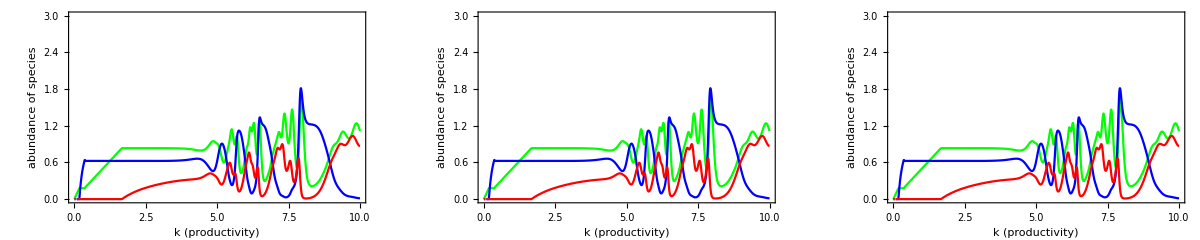

```mathematica
GraphicsGrid[{{
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
,
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
}}]
```

### Final densities of RNP across naivete towards N (ρ)

```mathematica
parsGoodρ =Delete[parsGoodH,Position[Keys[parsGoodH],ρ]];

finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsGoodρ},{R,Ν, P, eΝ, eP},{t,0,500}, {ρ}];

(* Note use to 1-ρ to reverse axis for visualization *)
Off[ParametricNDSolve::prange]

finalρR = Plot[Evaluate[R[1-ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Green} ,
PlotRange->{{0,1},{0,2}}];
finalρΝ = Plot[Evaluate[Ν[1-ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Blue}, 
PlotRange->{{0,1},{0,2}}];
finalρP = Plot[Evaluate[P[1-ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.015], Red}, 
PlotRange->{{0,1},{0,2}}];
finalρeΝ = Plot[Evaluate[eΝ[1-ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.0075], Dashed, Blue}, 
PlotRange->{{0,1},{0,2}}];
finalρeP = Plot[Evaluate[eP[1-ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thickness[0.0075], Dashed,  Red}, 
PlotRange->{{0,1},{0,2}}];

On[ParametricNDSolve::prange]
```

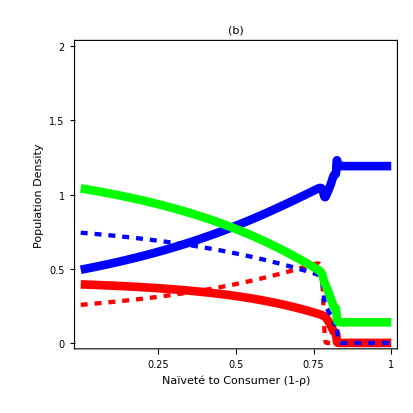

```mathematica
Fig7b = Show[ finalρP, finalρeP,finalρΝ,finalρeΝ,finalρR, Frame-> True, 
PlotLabel -> Style["(b)                                                                                       ", FontSize->14,  Bold],
FrameLabel->{"Naïveté to Consumer (1-ρ)","Population Density", "","Defense Effort"},  
AspectRatio -> 1/1, ImageSize -> 414,Spacings -> 30,LabelStyle-> {Black, Larger}, 
FrameTicks->{{{0,0.5,1, 1.5, 2},{0,0.5,1, 1.5, 2}},{{1, 0.75, 0.5,0.25}, {None}}}]
Save["Figs/temp/Fig7b.mx",Fig7b]
```

Determine equilibria

```mathematica
Get["Figs/temp/equil_naiveN.mx"];
```

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
Save["Figs/temp/equil_naiveN.mx",equil];
Join[Transpose[Range[Dimensions[equil]]],equil,2]//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1 | R→-(-1+c0) k r | Ν→0 | P→0 | eP→1-eΝ | 
2 | R→0 | Ν→0 | P→0 | eP→1-eΝ | 
3 | R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
4 | R→(k (aΝR (-1+fΝ) mP+aPR bPΝ mΝ-aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k) | Ν→(-aPR k (aΝR bΝR (-1+fΝ) mP+aPR bPR mΝ)+aPΝ (mP+aPR bPR (-1+c0) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | P→(-aPΝ bPΝ mΝ+aΝR (-1+fΝ) k (-aΝR bΝR (-1+fΝ) mP-aPR bPR mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fΝ) k)) | eΝ→1 | eP→0
5 | R→(-aPΝ bPΝ c0 r+aΝR fΝ mP ρ)/(aPR aΝR bPR fΝ ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(-aPΝ^2 bPΝ^2 bΝR c0^2 r^2+aPΝ aΝR bPΝ bΝR c0 r (2 fΝ mP+aPR bPR (c0-fΝ) k r) ρ+aΝR fΝ ρ (-aΝR bΝR fΝ mP^2 ρ+aPR bPR k r (aPR bPR c0 mΝ (-1+ρ)+aΝR bΝR (-c0+fΝ) mP ρ)))/(aPR^2 aΝR bPR fΝ k ρ (aΝR bΝR fΝ mP ρ+aPΝ c0 r (bPR-bPΝ bΝR-bPR ρ))) | eΝ→(-aPΝ c0 (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) r+aΝR fΝ (aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r)) ρ)/(aPR aΝR fΝ k (aΝR bΝR fΝ mP ρ+aPΝ c0 r (bPR-bPΝ bΝR-bPR ρ))) | eP→0
6 | R→mP/(aPR bPR) | Ν→0 | P→(-mP/(bPR k)+aPR r)/aPR^2 | eΝ→0 | eP→0
7 | R→mP/(aPR bPR) | Ν→0 | P→-(mP+aPR bPR (-1+c0) k r)/(aPR^2 bPR k) | eΝ→1 | eP→0
8 | R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(-mP+aPR bPR (-1+c0) (-1+fP) k r)/(aPR^2 bPR (-1+fP)^2 k) | eΝ→0 | eP→1
9 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1-1/fP+mP/(aPR bPR fP k r-aPR bPR c0 fP k r) | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
10 | R→((-c0+fP) k r)/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→1/fP+mP/(aPR bPR c0 k r-aPR bPR fP k r)
11 | R→-(k (aΝR mP+aPR bPΝ (-1+fP) mΝ+aPΝ bPΝ (-1+c0) r))/(aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k) | Ν→(-aPR (-1+fP) k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ)+aPΝ (mP+aPR bPR (-1+c0+fP-c0 fP) k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPR bPR (-1+fP) mΝ+aPΝ bPΝ bΝR (-1+c0) r))/(aPΝ (aPΝ bPΝ+aPR aΝR (bPR-bPΝ bΝR) (-1+fP) k)) | eΝ→0 | eP→1
12 | R→(aPR fP mΝ+aPΝ c0 r)/(aPR aΝR bΝR fP) | Ν→(-aPR fP mΝ-aPΝ c0 r+aPR aΝR bΝR (-c0+fP) k r)/(aPR aΝR^2 bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPR fP (-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ))+aPΝ (-aPΝ bPΝ c0+aPR aΝR (bPR c0+bPΝ bΝR (-c0+fP)) k) r)/(aPR aΝR bPR fP k (aPR fP mΝ+aPΝ c0 r))
13 | R→mΝ/(aΝR bΝR) | Ν→(-mΝ/(bΝR k)+aΝR r)/aΝR^2 | P→0 | eΝ→0 | eP→0
14 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
15 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→0 | eP→1
16 | R→mΝ/(aΝR bΝR) | Ν→-(mΝ+aΝR bΝR (-1+c0) k r)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
17 | R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(-mΝ+aΝR bΝR (-1+c0) (-1+fΝ) k r)/(aΝR^2 bΝR (-1+fΝ)^2 k) | P→0 | eΝ→1 | eP→0
18 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→1-1/fΝ+mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)
19 | R→-(c0 k r-fΝ k r-(√k √r √(-4 c0 fΝ mΝ+(4 c0 fΝ mΝ+aΝR bΝR (c0-fΝ)^2 k r) ρ))/(√aΝR √bΝR √ρ))/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→(c0 (-2+ρ)+fΝ ρ-(√ρ √(-4 c0 fΝ mΝ+(4 c0 fΝ mΝ+aΝR bΝR (c0-fΝ)^2 k r) ρ))/(√aΝR √bΝR √k √r))/(2 c0 fΝ (-1+ρ)) | eP→0
20 | R→-(c0 k r-fΝ k r+(√k √r √(-4 c0 fΝ mΝ+(4 c0 fΝ mΝ+aΝR bΝR (c0-fΝ)^2 k r) ρ))/(√aΝR √bΝR √ρ))/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→(c0 (-2+ρ)+fΝ ρ+(√ρ √(-4 c0 fΝ mΝ+(4 c0 fΝ mΝ+aΝR bΝR (c0-fΝ)^2 k r) ρ))/(√aΝR √bΝR √k √r))/(2 c0 fΝ (-1+ρ)) | eP→0
21 | R→(aPR aΝR fΝ k (aΝR bΝR (-fP+(-1+fP) fΝ) mP (bPΝ bΝR+bPR (-2+ρ)) ρ-aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)^2)-aPR^2 aΝR bPR fP (fP (-1+fΝ)-fΝ) k mΝ (bPR ρ+bPΝ (bΝR-2 bΝR ρ))+(bPΝ bΝR-bPR ρ) √(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2)))))/(2 aPR aΝR (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | Ν→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (bPΝ bΝR-bPR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) (-aPR aΝR (fP (-1+fΝ)-fΝ) k (aPR bPR fP mΝ+aΝR bΝR fΝ mP ρ)+√(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2))))))/(2 aPΝ aΝR fΝ (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | P→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) ρ (bPΝ bΝR-bPR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) ρ (-aPR aΝR (fP (-1+fΝ)-fΝ) k (aPR bPR fP mΝ+aΝR bΝR fΝ mP ρ)+√(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2))))))/(2 aPR aPΝ fP (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | eΝ→(aPR^2 aΝR bPR fP k mΝ (fΝ-fP (1+fΝ)+2 (-1+fP) fΝ ρ)+aPR aΝR fΝ k (-aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)+aΝR bΝR mP (-fΝ ρ+fP (-2+ρ+fΝ ρ)))-√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPR fP (-aPΝ bPΝ mΝ-aΝR bΝR k (aΝR mP+aPΝ bPΝ (-1+c0) r))-aPΝ aΝR fΝ mP ρ+aPR aΝR (-1+fP) fΝ k (aΝR bΝR mP+aPΝ bPR (-1+c0) r) ρ+aPR^2 aΝR bPR (-1+fP) k mΝ (-fP+(-1+fP) fΝ ρ))+aPR aΝR k (aΝR bΝR fΝ mP (fΝ ρ-fP (-2+ρ+fΝ ρ))+fP (aPΝ (-1+c0) fΝ r (bPΝ bΝR-bPR ρ)+aPR bPR mΝ (fP-fΝ+fP fΝ-2 (-1+fP) fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ)) | eP→(aPR^2 aΝR bPR fP k mΝ (fP-fP fΝ+fΝ (-1+2 ρ))+aPR aΝR fΝ k (aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)+aΝR bΝR mP (fP (-1+fΝ) (-2+ρ)+fΝ ρ))+√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPR fP (-aPΝ bPΝ mΝ-aΝR bΝR k (aΝR mP+aPΝ bPΝ (-1+c0) r))-aPΝ aΝR fΝ mP ρ+aPR aΝR (-1+fP) fΝ k (aΝR bΝR mP+aPΝ bPR (-1+c0) r) ρ+aPR^2 aΝR bPR (-1+fP) k mΝ (-fP+(-1+fP) fΝ ρ))+aPR aΝR k (aΝR bΝR fΝ mP (fΝ ρ-fP (-2+ρ+fΝ ρ))+fP (aPΝ (-1+c0) fΝ r (bPΝ bΝR-bPR ρ)+aPR bPR mΝ (fP-fΝ+fP fΝ-2 (-1+fP) fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ))
22 | R→(aPR aΝR fΝ k (aΝR bΝR (-fP+(-1+fP) fΝ) mP (bPΝ bΝR+bPR (-2+ρ)) ρ-aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)^2)-aPR^2 aΝR bPR fP (fP (-1+fΝ)-fΝ) k mΝ (bPR ρ+bPΝ (bΝR-2 bΝR ρ))+(-bPΝ bΝR+bPR ρ) √(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2)))))/(2 aPR aΝR (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | Ν→(aPΝ fP fΝ (2 aPR bPR fP mΝ+aΝR bΝR (2 fΝ mP-aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (bPΝ bΝR-bPR ρ)-bPR bΝR (fP (-1+fΝ)-fΝ) (aPR aΝR (fP (-1+fΝ)-fΝ) k (aPR bPR fP mΝ+aΝR bΝR fΝ mP ρ)+√(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2))))))/(2 aPΝ aΝR fΝ (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | P→-(ρ (aPΝ fP fΝ (-2 aPR bPR fP mΝ+aΝR bΝR (-2 fΝ mP+aPR bPR (-1+c0) (-fP+(-1+fP) fΝ) k r)) (bPΝ bΝR-bPR ρ)+bPR bΝR (fP (-1+fΝ)-fΝ) (aPR aΝR (fP (-1+fΝ)-fΝ) k (aPR bPR fP mΝ+aΝR bΝR fΝ mP ρ)+√(aPR aΝR k (aPR^3 aΝR bPR^2 fP^2 (fP+fΝ-fP fΝ)^2 k mΝ^2+4 aPΝ aΝR^2 bΝR fP fΝ^3 mP^2 (-1+ρ) ρ+2 aPR^2 bPR fP fΝ mΝ (aΝR^2 bΝR (fP+fΝ-fP fΝ)^2 k mP ρ+aPΝ fP (-2 bPΝ fP mΝ+aΝR bPΝ bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r+(2 bPΝ fP mΝ+aΝR (bPR-2 bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ))+aPR aΝR fΝ^2 (aΝR^2 bΝR^2 (fP+fΝ-fP fΝ)^2 k mP^2 ρ^2+aPΝ^2 (-1+c0)^2 fP^2 k r^2 (bPΝ bΝR-bPR ρ)^2-2 aPΝ fP mP (2 bPΝ bΝR fP mΝ+(2 (bPR-bPΝ bΝR) fP mΝ+aΝR bΝR (-2 bPR+bPΝ bΝR) (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ+bPR (-2 fP mΝ+aΝR bΝR (-1+c0) (-fP+(-1+fP) fΝ) k r) ρ^2)))))))/(2 aPR aPΝ fP (aPR aΝR bPR bΝR (bPR-bPΝ bΝR) (fP+fΝ-fP fΝ)^2 k ρ+aPΝ fP fΝ (bPΝ bΝR-bPR ρ)^2)) | eΝ→(aPR^2 aΝR bPR fP k mΝ (fΝ-fP (1+fΝ)+2 (-1+fP) fΝ ρ)+aPR aΝR fΝ k (-aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)+aΝR bΝR mP (-fΝ ρ+fP (-2+ρ+fΝ ρ)))+√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPR fP (-aPΝ bPΝ mΝ-aΝR bΝR k (aΝR mP+aPΝ bPΝ (-1+c0) r))-aPΝ aΝR fΝ mP ρ+aPR aΝR (-1+fP) fΝ k (aΝR bΝR mP+aPΝ bPR (-1+c0) r) ρ+aPR^2 aΝR bPR (-1+fP) k mΝ (-fP+(-1+fP) fΝ ρ))+aPR aΝR k (aΝR bΝR fΝ mP (fΝ ρ-fP (-2+ρ+fΝ ρ))+fP (aPΝ (-1+c0) fΝ r (bPΝ bΝR-bPR ρ)+aPR bPR mΝ (fP-fΝ+fP fΝ-2 (-1+fP) fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ)) | eP→(aPR^2 aΝR bPR fP k mΝ (fP-fP fΝ+fΝ (-1+2 ρ))+aPR aΝR fΝ k (aPΝ (-1+c0) fP r (bPΝ bΝR-bPR ρ)+aΝR bΝR mP (fP (-1+fΝ) (-2+ρ)+fΝ ρ))-√(aPR aΝR k (-4 fP fΝ (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ) (aPR fP (-aPΝ bPΝ mΝ-aΝR bΝR k (aΝR mP+aPΝ bPΝ (-1+c0) r))-aPΝ aΝR fΝ mP ρ+aPR aΝR (-1+fP) fΝ k (aΝR bΝR mP+aPΝ bPR (-1+c0) r) ρ+aPR^2 aΝR bPR (-1+fP) k mΝ (-fP+(-1+fP) fΝ ρ))+aPR aΝR k (aΝR bΝR fΝ mP (fΝ ρ-fP (-2+ρ+fΝ ρ))+fP (aPΝ (-1+c0) fΝ r (bPΝ bΝR-bPR ρ)+aPR bPR mΝ (fP-fΝ+fP fΝ-2 (-1+fP) fΝ ρ)))^2)))/(2 aPR aΝR fP fΝ k (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-1+ρ))
23 | R→(-aPR aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) k r ρ+√(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bΝR fP fΝ^2 ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aPR aΝR bΝR fΝ k r (c0 fP (-2+ρ)-c0 fΝ ρ+fP fΝ ρ)-√(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bΝR c0 fP fΝ^2 k r (-1+ρ)) | eP→(2 aPR^2 aΝR bPR c0 fP fΝ^2 k mΝ r (-1+ρ) ρ+aPR aΝR fΝ k r ρ (aPΝ c0 r (bPΝ bΝR (-fP fΝ+c0 (fP+fΝ))+2 bPR c0 fΝ (-1+ρ))-aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) mP ρ)+(aPΝ bPΝ c0 r-aΝR fΝ mP ρ) √(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR c0 fP fΝ^2 k r (aPR fP mΝ+aPΝ c0 r) (-1+ρ) ρ)
24 | R→-(aPR aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) k r ρ+√(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bΝR fP fΝ^2 ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aPR aΝR bΝR fΝ k r (c0 fP (-2+ρ)-c0 fΝ ρ+fP fΝ ρ)+√(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bΝR c0 fP fΝ^2 k r (-1+ρ)) | eP→(2 aPR^2 aΝR bPR c0 fP fΝ^2 k mΝ r (-1+ρ) ρ+aPR aΝR fΝ k r ρ (aPΝ c0 r (bPΝ bΝR (-fP fΝ+c0 (fP+fΝ))+2 bPR c0 fΝ (-1+ρ))-aΝR bΝR fΝ (-fP fΝ+c0 (fP+fΝ)) mP ρ)+(-aPΝ bPΝ c0 r+aΝR fΝ mP ρ) √(aPR aΝR bΝR fΝ^2 k r ρ (-4 aPR c0 fP^2 fΝ mΝ+4 aPΝ c0^2 fP fΝ r (-1+ρ)+aPR (4 c0 fP^2 fΝ mΝ+aΝR bΝR (fP fΝ-c0 (fP+fΝ))^2 k r) ρ)))/(2 aPR aΝR bPR c0 fP fΝ^2 k r (aPR fP mΝ+aPΝ c0 r) (-1+ρ) ρ)
25 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
26 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
27 | R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
28 | R→(k (-aΝR mP+aPR bPΝ mΝ+aPΝ bPΝ r))/(aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | P→(-aPΝ bPΝ mΝ+aΝR k (-aΝR bΝR mP+aPR bPR mΝ+aPΝ bPΝ bΝR r))/(aPΝ (aPΝ bPΝ+aPR aΝR (-bPR+bPΝ bΝR) k)) | eΝ→0 | eP→0
29 | R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
30 | R→-(-1+c0) k r | Ν→0 | P→0 | eΝ→1 | eP→0
31 | R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Determine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν) | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν | -aPΝ Ν | 0
0 | -aΝR (-1+eΝ) eΝ fΝ v ρ | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν ρ) | -aPR eP eΝ fP v | eΝ (-aPR fP P+c0 r) v
aPR bPR (1-eP fP) P | aPΝ bPΝ P | 0 | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aΝR eP eΝ fΝ v ρ | eP v (c0 r-aΝR fΝ Ν ρ) | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν ρ))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aΝR (-1+eΝ fΝ) R | R (-c0 r+aΝR fΝ Ν)
aΝR bΝR (1-eΝ fΝ) Ν | -mΝ-aPΝ P+aΝR bΝR (1-eΝ fΝ) R | -aΝR bΝR fΝ R Ν
0 | -aΝR (-1+eΝ) eΝ fΝ v ρ | v (-aPR eP fP P+c0 (-1+eP+2 eΝ) r+aΝR (1-2 eΝ) fΝ Ν ρ))

(aPR (-1+eP fP) P+r-c0 (eP+eΝ) r-(2 R)/k+aΝR (-1+eΝ fΝ) Ν | aPR (-1+eP fP) R | (aPR fP P-c0 r) R
aPR bPR (1-eP fP) P | -mP+aPR bPR (1-eP fP) R+aPΝ bPΝ Ν | -aPR bPR fP P R
0 | -aPR (-1+eP) eP fP v | v (aPR (1-2 eP) fP P+c0 (-1+2 eP+eΝ) r-aΝR eΝ fΝ Ν ρ))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subparsH=Delete[parsExcH,Position[Keys[parsExcH],k]];
subparsM=Delete[parsExcM,Position[Keys[parsExcM],k]];
subparsL=Delete[parsExcL,Position[Keys[parsExcL],k]];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq13RΝ=JRΝ/.equil[[13,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsH],#≥0&];
AllFeas8[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsH],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsH],#≥0&];
AllFeas13[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsH],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas13M[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas13L[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]];pReEig13RΝ[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsH]]]];

pReEig13RΝM[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];
pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]];

pReEig13RΝL[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsL]]]] ;
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]];
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsH]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsH]]]];
pReEig8RP[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsH]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];
pReEig8RPM[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
pReEig8RPL[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsExcH, {{2},{7}}];
kaPΝparsM = Delete[parsExcM, {{2},{7}}];
kaPΝparsL = Delete[parsExcL, {{2},{7}}];
```

```mathematica
RstarRN13 = equil[[13,1,2]];
NstarRN13= equil[[13,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN13 = bPR aPR (1 -0*fP)RstarRN13  + aPN bPΝ NstarRN13 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
```

#### P invades RΝ

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13kaPN = plotPinvRN13/.kaPΝparsH;
PlotRN13 = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], Exclusions->{Solve[Denominator[PinvRN13kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig13RΝ[x]<0&&AllFeas13[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,2.45}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
Rstar8 = equil[[8,1,2]];
Pstar8= equil[[8,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv10 = bΝR aΝR (1 -0*fΝ)Rstar10  - aPΝ Pstar10 - mΝ;
Νinv8= bΝR aΝR (1 -0*fΝ)Rstar8 - aPΝ Pstar8 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8kaPN = plotΝinv8/.kaPΝparsH;
PlotRP8 = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

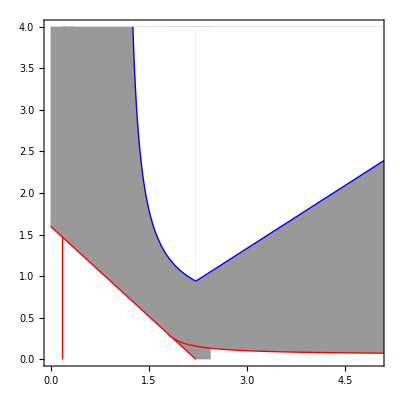

```mathematica
Fig5aa = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8,
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,4}},LabelStyle-> Larger]
(*Save["Figs/temp/Fig5aa.mx",Fig5aa]*)
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsM;
PlotRN13M = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],Exclusions->{Solve[Denominator[PinvRN13kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig13RΝM[x]<0&&AllFeas13M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19M = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17M = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6M = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10M = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsM;
PlotRP8M = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

```mathematica
equilP= equil/.kaPΝparsM;
Jeq=J/.equil/.kaPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig5dReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,5},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,5},{0,2}}]
Save["Figs/temp/Fig5dReg.mx",Fig5dReg]
```

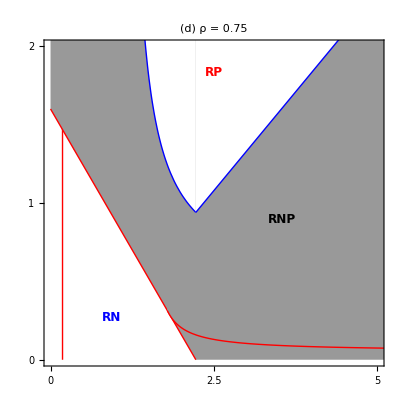

```mathematica
Fig5d =Show[PlotRN13M, PlotRN19M,PlotRN17M,PlotRP6M,PlotRP10M, PlotRP8M, Fig5dReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.2,0.15}]]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,2.5,5}, {None}}}]
Save["Figs/temp/Fig5d.mx",Fig5d]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsL;
PlotRN13L = Plot[PinvRN13kaPN,{k, 0.2,5},  PlotRange->{{0,5},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5], Exclusions->{Solve[Denominator[PinvRN13kaPN]==0,k][[1,1]]},
RegionFunction->Function[{x},pReEig13RΝL[x]<0&&AllFeas13L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19L = Plot[PinvRN19kaPN,{k, 0,4}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5]];

PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17L = Plot[PinvRN17kaPN,{k, 0,5}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.5]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k,  1.112,5}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig6RPL[x]<0&&AllFeas6L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,5}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsL;
PlotRP8L =PlotRP8L = Plot[Νinv8kaPN,{k, 0,5}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];
```

```mathematica
equilP= equil/.kaPΝparsL;
Jeq=J/.equil/.kaPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig5eReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{k,0,5},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,5},{0,2}}]
Save["Figs/temp/Fig5eReg.mx",Fig5eReg]
```

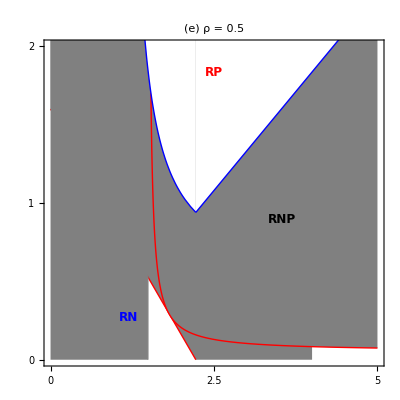

```mathematica
Fig5e =Show[PlotRN13L, PlotRN19L,PlotRN17L,PlotRP6L,PlotRP10L, PlotRP8L,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.7,0.45}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.25,0.15}]]}],
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,5},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,2.5,5}, {None}}}]
Save["Figs/temp/Fig5e.mx",Fig5e]
```

```mathematica
igpN=
Show[
Graphics[{{GrayLevel[0],Thickness[0.05],
Line[{{0.1, 0.1},{.6,.6}}], 
Line[{{0.6, 0.6},{0,1}}], 
Line[{{0.1, 0.1},{0,1}}] 
}}],
Graphics[{{GrayLevel[0.5],Disk[{.1,.1},.2]},{GrayLevel[0.5], Disk[{.6,.6},.2]}, {GrayLevel[0.5],Disk[{0,1.0},.2]}, {Blue,Thickness[0.04],Circle[{0.6,0.6},.18]}, 
{Black,Thickness[0.01],Circle[{0.1,0.1},.2]}, 
{Black,Thickness[0.01],Circle[{0,1},.2]}}],
Graphics[{Text[Style["R",16,Black , Bold],{0.1,0.1}], 
Text[Style["N",16,Black , Bold],{0.6,0.6}],
Text[Style["P",16,Black , Bold],{0,1}]}]]
Save["Figs/temp/igpN.mx",igpN]
```

### Invasibility Plot (c0 and aPN)

### Functions for working with equilibrium values across a gradient of cost (c0)

```mathematica
subparsH=Delete[parsExcH,Position[Keys[parsExcH],c0]];
subparsM=Delete[parsExcM,Position[Keys[parsExcM],c0]];
subparsL=Delete[parsExcL,Position[Keys[parsExcL],c0]];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq13RΝ=JRΝ/.equil[[13,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsH],#≥0&];
AllFeas8[c0_]=AllTrue[Re[equil[[8,All,2]]/.subparsH],#≥0&];
AllFeas10[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsH],#≥0&];
AllFeas13[c0_]=AllTrue[Re[equil[[13,All,2]]/.subparsH],#≥0&];
AllFeas17[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsH],#≥0&];
AllFeas19[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsH],#≥0&];

AllFeas6M[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[c0_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas10M[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas13M[c0_]=AllTrue[Re[equil[[13,All,2]]/.subparsM],#≥0&];
AllFeas17M[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];

AllFeas6L[c0_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[c0_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas10L[c0_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas13L[c0_]=AllTrue[Re[equil[[13,All,2]]/.subparsL],#≥0&];
AllFeas17L[c0_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[c0_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
```

```mathematica
pReEig19RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsH]]]];pReEig17RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsH]]]];pReEig13RΝ[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsH]]]];

pReEig13RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsM]]]];
pReEig19RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];
pReEig17RΝM[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]];

pReEig13RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsL]]]] ;
pReEig19RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
pReEig17RΝL[c0_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsH]]]];
pReEig10RP[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsH]]]];
pReEig8RP[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsH]]]];

pReEig6RPM[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig10RPM[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];
pReEig8RPM[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[c0_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig10RPL[c0_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
pReEig8RPL[c0_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

#### P invades RN

```mathematica
c0aPΝparsH= Delete[parsExcH,Position[Keys[parsExcH],c0|aPΝ ]];
c0aPΝparsM=Delete[parsExcM,Position[Keys[parsExcM],c0|aPΝ ]];
c0aPΝparsL=Delete[parsExcL,Position[Keys[parsExcL],c0|aPΝ ]];
```

#### High Recognition (ρ = 1)

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsH;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝ[x]<0&&AllFeas13[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsH;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsH;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsH;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsH;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsH;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsH;
Jeq=J/.equil/.c0aPΝparsH/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6aaReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
(*Save["Figs/temp/Fig6aaReg.mx",Fig6aaReg*)
```

```mathematica
Fig6aa = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Fig6aaReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
PlotLabel -> Style["", FontSize->12,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{None}, {None}}}]
(*Save["Figs/temp/Fig6aa.mx",Fig6aa]*)
```

#### Medium naivete (ρ = 0.75)

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsM;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝM[x]<0&&AllFeas13M[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsM;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,0.56}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsM;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,0.56}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsM;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsM;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsM;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsM;
Jeq=J/.equil/.c0aPΝparsM/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6dReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig6dReg.mx",Fig6dReg]
```

```mathematica
Fig6d = Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Fig6dReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.7,0.8}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.75,0.2}]]}],
Graphics[{Red,Thick,
Line[{{0.56,0.72},{0.56,0.42}}]}],
PlotLabel -> Style["(d)    ρ = 0.75", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,0.5, 1}, {None}}}]
Save["Figs/temp/Fig6d.mx",Fig6d]
```

#### Low recognition (ρ = 0.5)

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6c0aPN = plotΝinv6/.c0aPΝparsL;
PlotRP6 = Plot[Νinv6c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10c0aPN = plotΝinv10/.c0aPΝparsL;
PlotRP10 = Plot[Νinv10c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8c0aPN = plotΝinv8/.c0aPΝparsL;
PlotRP8 = Plot[Νinv8c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle-> White,   
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];

plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13c0aPN = plotPinvRN13/.c0aPΝparsL;
PlotRN13 = Plot[PinvRN13c0aPN,{c0, 0,1}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig13RΝL[x]<0&&AllFeas13L[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19c0aPN = plotPinvRN19/.c0aPΝparsL;
PlotRN19 = Plot[PinvRN19c0aPN,{c0, 0,0.372}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17c0aPN = plotPinvRN17/.c0aPΝparsL;
PlotRN17 = Plot[PinvRN17c0aPN,{c0, 0,0.372}, PlotRange->{{0,1},{0,2}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.5], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];
```

```mathematica
equilP= equil/.c0aPΝparsL;
Jeq=J/.equil/.c0aPΝparsL/.eP-> 0;
domEigs=Max/@Re/@Eigenvalues/@Jeq/.eP-> 0;
```

```mathematica
Fig6eReg = RegionPlot[
Evaluate[Not[Apply[Or,Thread[domEigs<0]/.{eP-> 0}]]],
{c0,0,1},{aPΝ,0,2},
Mesh->25,MeshFunctions->{#1+#2&,#1-#2&},
PlotStyle-> Gray,MeshStyle->White,
MaxRecursion->3,
BoundaryStyle->None,
PlotRange->{{0,1},{0,2}}]
Save["Figs/temp/Fig6eReg.mx",Fig6eReg]
```

```mathematica
Fig6e =Show[ PlotRN19, PlotRN17, PlotRN13,PlotRP6,PlotRP10, PlotRP8, Fig6eReg,
Graphics[{Text[Style["RNP",12,Black , Bold],Scaled[{0.2,0.6}]],
Text[Style["RP",12,Red , Bold],Scaled[{0.5,0.9}]],
Text[Style["RN",12,Blue, Bold ],Scaled[{0.65,0.15}]]}],
Graphics[{Red,Thick,
Line[{{0.37,0.72},{0.37,0.115}}]}],
PlotLabel -> Style["(e)    ρ = 0.5", FontSize->14,  Bold],
Frame->True, AspectRatio -> 1/1, PlotRange->{{0,1},{0,2}},FrameTicks->{{{0,1, 2},{None}},{{0,0.5, 1}, {None}}}]
Save["Figs/temp/Fig6e.mx",Fig6e]
```

## Combine all export all plots to TIFF

```mathematica
SetDirectory[NotebookDirectory[]]

files=FileNames["*.mx","Figs/temp/"] (* Get list of all temporary plot files *)
Get[#]&/@files; (* Load all their contents (plot variable definitions) *)
```

/Users/marknovak/Git/IGP-adaptive-defense

{Figs/temp/equil_naiveN.mx,Figs/temp/equil_naiveP.mx,Figs/temp/equil_suboptN.mx,Figs/temp/equil_suboptP.mx,Figs/temp/Fig1.mx,Figs/temp/Fig2a.mx,Figs/temp/Fig2aReg.mx,Figs/temp/Fig2b.mx,Figs/temp/Fig2bReg.mx,Figs/temp/Fig2c.mx,Figs/temp/Fig2cReg.mx,Figs/temp/Fig2d.mx,Figs/temp/Fig2dReg.mx,Figs/temp/Fig2e.mx,Figs/temp/Fig2eReg.mx,Figs/temp/Fig3a.mx,Figs/temp/Fig3aReg.mx,Figs/temp/Fig3b.mx,Figs/temp/Fig3bReg.mx,Figs/temp/Fig3c.mx,Figs/temp/Fig3cReg.mx,Figs/temp/Fig3d.mx,Figs/temp/Fig3dReg.mx,Figs/temp/Fig3e.mx,Figs/temp/Fig3eReg.mx,Figs/temp/Fig4a.mx,Figs/temp/Fig4b.mx,Figs/temp/Fig5a.mx,Figs/temp/Fig5aReg.mx,Figs/temp/Fig5b.mx,Figs/temp/Fig5bReg.mx,Figs/temp/Fig5c.mx,Figs/temp/Fig5cReg.mx,Figs/temp/Fig5d.mx,Figs/temp/Fig5dReg.mx,Figs/temp/Fig5e.mx,Figs/temp/Fig5eReg.mx,Figs/temp/Fig6a.mx,Figs/temp/Fig6aReg.mx,Figs/temp/Fig6b.mx,Figs/temp/Fig6bReg.mx,Figs/temp/Fig6c.mx,Figs/temp/Fig6cReg.mx,Figs/temp/Fig6d.mx,Figs/temp/Fig6dReg.mx,Figs/temp/Fig6e.mx,Figs/temp/Fig6eReg.mx,Figs/temp/Fig7a.mx,Figs/temp/Fig7b.mx,Figs/temp/Fig8.mx,Figs/temp/igpN.mx,Figs/temp/igpO.mx}

Show::gcomb: Could not combine the graphics objects in ….

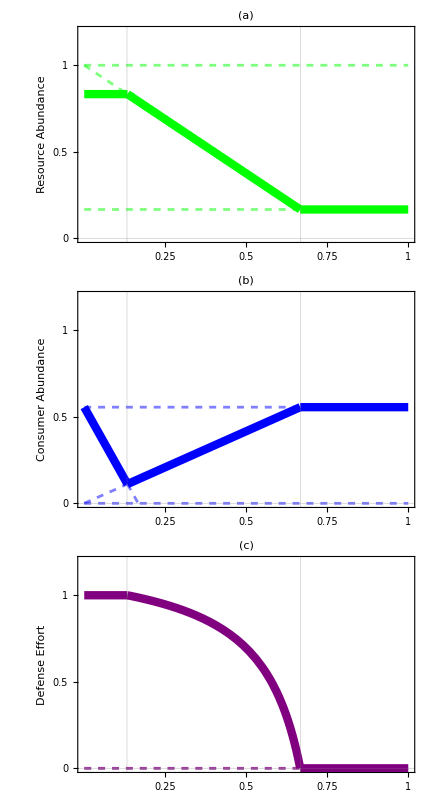
-Graphics-Cost of Defense

Figs/MoNSTR_Fig1_Full.tiff

```mathematica
Fig1
Export["Figs/MoNSTR_Fig1_Full.tiff",Fig1, "TIFF",ImageResolution->600]
```

```mathematica
Figure2abcde = Panel[GraphicsGrid[{{Fig2a,Fig2b, Fig2c},{igpO, Fig2d, Fig2e}}, ImageSize-> 518, Spacings->{0,20}],
 {"Productivity",Rotate["IGP strength",Pi/2]},
{Bottom,Left},Background->White, LabelStyle->{Large}]
Export["Figs/MoNSTR_Fig2_Full.tiff",Figure2abcde,"TIFF", ImageResolution->600]
```

-Graphics-ProductivityIGP strength

Figs/MoNSTR_Fig2_Full.tiff

```mathematica
Figure3abcde = Panel[GraphicsGrid[{{Fig3a,Fig3b, Fig3c},{igpO, Fig3d, Fig3e}}, 
ImageSize-> 518, Spacings->{0,20}], {"Cost of Defense",Rotate["IGP strength",Pi/2]},
{Bottom,Left},Background->White, LabelStyle->{Large}]
Export["Figs/MoNSTR_Fig3_Full.tiff",Figure3abcde,"TIFF", ImageResolution->600]
```

-Graphics-Cost of DefenseIGP strength

Figs/MoNSTR_Fig3_Full.tiff

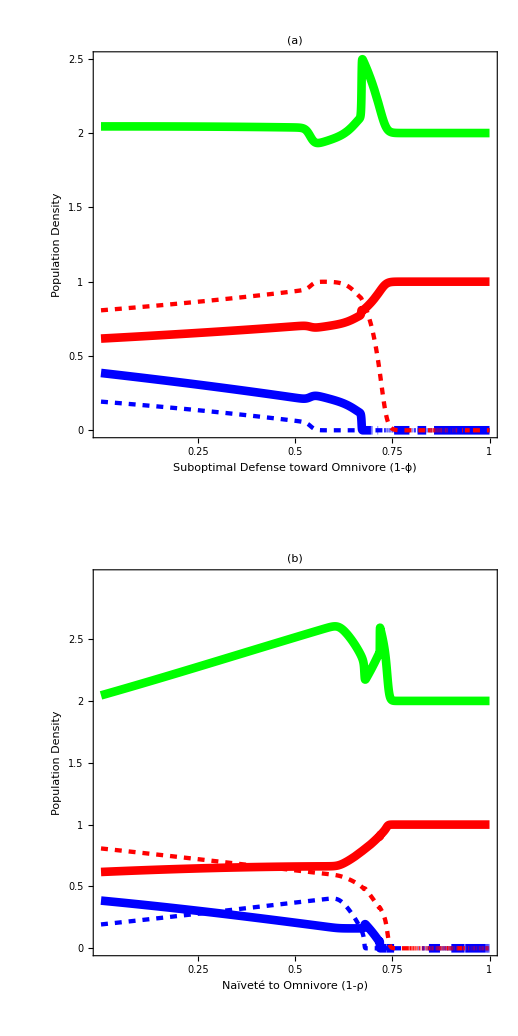
-Graphics-Novelty Gradient

Figs/MoNSTR_Fig4_Full.tiff

```mathematica
Fig4ab =  Panel[GraphicsColumn[{Fig4a,Fig4b}, ImageSize-> 518, Spacings->0], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
Export["Figs/MoNSTR_Fig4_Full.tiff",Fig4ab,"TIFF", ImageResolution-> 600]
```

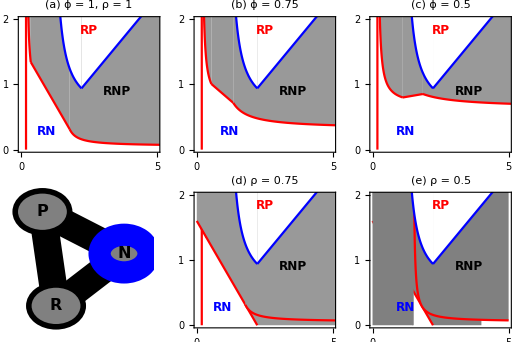
-Graphics-ProductivityIGP strength

Figs/MoNSTR_Fig5_Full.tiff

```mathematica
Figure5abcde = Panel[GraphicsGrid[{{Fig5a,Fig5b, Fig5c},{igpN, Fig5d, Fig5e}}, ImageSize-> 518, Spacings->{20,20}], {"Productivity",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
Export["Figs/MoNSTR_Fig5_Full.tiff",Figure5abcde,"TIFF", ImageResolution->600]
```

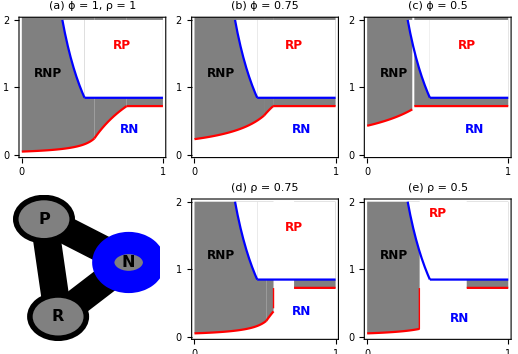
-Graphics-Defense CostIGP strength

Figs/MoNSTR_Fig6_Full.tiff

```mathematica
Figure6abcde = Panel[GraphicsGrid[{{Fig6a,Fig6b, Fig6c},{igpN, Fig6d, Fig6e}}, ImageSize-> 518, Spacings->{0,20}], {"Defense Cost",Rotate["IGP strength",Pi/2]},{Bottom,Left},Background->White, LabelStyle->{Large}]
Export["Figs/MoNSTR_Fig6_Full.tiff",Figure6abcde,"TIFF", ImageResolution->600]
```

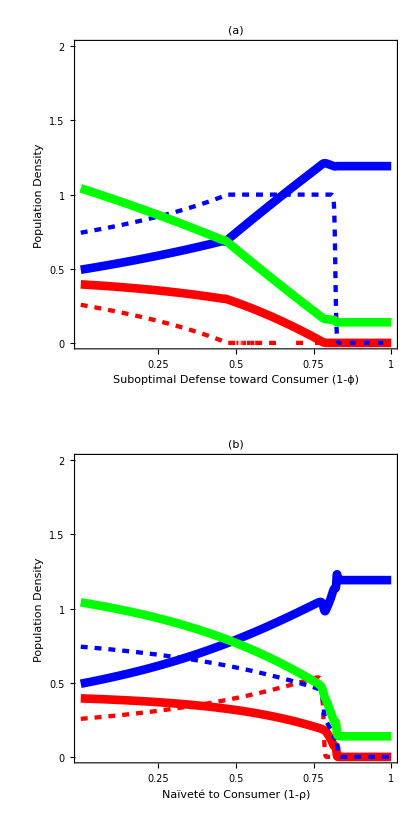
-Graphics-Novelty Gradient

Figs/MoNSTR_Fig7_Full.tiff

```mathematica
Fig7ab =  Panel[GraphicsColumn[{Fig7a,Fig7b}, ImageSize-> 414, Spacings->0], 
{"Novelty Gradient",Rotate["",Pi/2]},{Bottom,Left},Background->White, LabelStyle->Large]
Export["Figs/MoNSTR_Fig7_Full.tiff",Fig7ab,"TIFF", ImageResolution-> 600]
```

```mathematica
Fig8
Export["Figs/MoNSTR_Fig8_Full.tiff",Fig8,"TIFF", ImageResolution-> 600]
```

-Graphics-

Figs/MoNSTR_Fig8_Full.tiff